# Definitions of functions.

```mathematica
<<FeynCalc`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

## Auxiliary functions

Here tensors that are used throughout the code are defined.

This command generates an array of a form {m1,n2, ... , mN,nN}.

```mathematica
dummyArray = Function[Flatten[Function[{ToExpression["m"<>ToString[#]],ToExpression["n"<>ToString[#]]}]/@Range[#]]];
```

Examples.

```mathematica
dummyArray[0]
dummyArray[1]
dummyArray[2]
dummyArray[3]
```

{}

{m1,n1}

{m1,n1,m2,n2}

{m1,n1,m2,n2,m3,n3}

This command takes a list of even number of elements, splits it in pairs, and make a metric of each pair.

```mathematica
MTDWrapper = Function[Times@@MTD@@@Partition[#,2]];
```

Examples.

```mathematica
MTDWrapper[dummyArray[1]]
MTDWrapper[dummyArray[2]]
MTDWrapper[dummyArray[3]]
```

g^m1n1

g^m1n1 g^m2n2

g^m1n1 g^m2n2 g^m3n3

This command takes two lists. The first one is the list to be symmetrized. The second one is a list of two elements. The result is a join list. Its first component it the original list; its second component is a list with the given elements begin swapped.

```mathematica
arraySymmetrization=Function[{array,argumets},Join[array,(array/.{argumets[[1]]->argumets[[2]],argumets[[2]]->argumets[[1]]})]];
```

Examples.

```mathematica
arraySymmetrization[Alphabet["Greek"],{"α","ω"}]
```

{α,β,γ,δ,ε,ζ,η,θ,ι,κ,λ,μ,ν,ξ,ο,π,ρ,σ,τ,υ,φ,χ,ψ,ω,ω,β,γ,δ,ε,ζ,η,θ,ι,κ,λ,μ,ν,ξ,ο,π,ρ,σ,τ,υ,φ,χ,ψ,α}

This function takes three arguments. The first one is a list, second and third are elements of the list that should be swapped. It returns a list with the elements swapped.

```mathematica
Swap=Function[#1/.{#2->#3,#3->#2}];
```

```mathematica
Alphabet["Greek"]
Swap[Alphabet["Greek"],"μ","ν"]
```

{α,β,γ,δ,ε,ζ,η,θ,ι,κ,λ,μ,ν,ξ,ο,π,ρ,σ,τ,υ,φ,χ,ψ,ω}

{α,β,γ,δ,ε,ζ,η,θ,ι,κ,λ,ν,μ,ξ,ο,π,ρ,σ,τ,υ,φ,χ,ψ,ω}

This function takes an array of even number of elements and symmetrized it with respect to each index pair.

```mathematica
SymmetrizeIndexPairs= Function[indexArray,If[Length[indexArray]≠0,Partition[Fold[Join[#1,Swap[#1,#2[[1]],#2[[2]]]]&][indexArray,Partition[indexArray,2]],Length[indexArray]],{{}}] ];
```

```mathematica
SymmetrizeIndexPairs[dummyArray[0]]
SymmetrizeIndexPairs[dummyArray[1]]
SymmetrizeIndexPairs[dummyArray[2]]
SymmetrizeIndexPairs[dummyArray[3]]
```

{{}}

(m1 | n1
n1 | m1)

(m1 | n1 | m2 | n2
n1 | m1 | m2 | n2
m1 | n1 | n2 | m2
n1 | m1 | n2 | m2)

(m1 | n1 | m2 | n2 | m3 | n3
n1 | m1 | m2 | n2 | m3 | n3
m1 | n1 | n2 | m2 | m3 | n3
n1 | m1 | n2 | m2 | m3 | n3
m1 | n1 | m2 | n2 | n3 | m3
n1 | m1 | m2 | n2 | n3 | m3
m1 | n1 | n2 | m2 | n3 | m3
n1 | m1 | n2 | m2 | n3 | m3)

## I tensor

Here the definition of the I tensor is given. The tensor is responsible for the perturbative structure of g^μν.

This cell provides the definition of the I tensor with index symmetries.

```mathematica
ITensor=Function[Total[1/Power[2,Length[#]/2] MTDWrapper[RotateLeft[#,1]]&/@SymmetrizeIndexPairs[#]]];
```

Examples.

```mathematica
ITensor[{}]
ITensor[{μ,ν}]
ITensor[{μ,ν,α,β}]
ITensor[{μ,ν,α,β,ρ,σ}]
```

1

g^μν

1/2 g^αν g^βμ+1/2 g^αμ g^βν

1/8 g^ασ g^βν g^μρ+1/8 g^αν g^βσ g^μρ+1/8 g^αρ g^βν g^μσ+1/8 g^αν g^βρ g^μσ+1/8 g^ασ g^βμ g^νρ+1/8 g^αμ g^βσ g^νρ+1/8 g^αρ g^βμ g^νσ+1/8 g^αμ g^βρ g^νσ

## C tensor

Here the definition of the C tensor is given. The tensor is responsible for the perturbative structure of √-g.

This cell generates a distribution of index pairs within a single term of the C tensor.

```mathematica
CTensorIndexDistrubution =Function[{n,m},Select[Tuples[Range[n],m],Total[#]==n&]];
```

This cell evaluates a single term with a m I tensors of the C tensor. N.B. The definition of the I tensor without any index symmetries is used!

```mathematica
CTensorTerm=Function[{indexArray,m},Total[((1/(Times@@#)Times@@(ITensor/@FoldPairList[TakeDrop,indexArray,2#])))&/@CTensorIndexDistrubution[Length[indexArray]/2,m]]];
```

This cell evaluates the C tensor definition without index symmetry.

```mathematica
CTensorCore =Function[indexArray,(Power[-1,Length[indexArray]/2+#]/(Factorial[#]Power[2,#])CTensorTerm[indexArray,#]&)/@Range[Length[indexArray]/2]//Total//Expand];
```

This cell generates an array of indices with all required symmetries.

```mathematica
CTensorIndex=Function[indexArray,Partition[Flatten[Permutations[Partition[indexArray,2]]],Length[indexArray]]  ];
```

This cell defined the C tensor with index symmetries.

```mathematica
CTensor =Function[indexArray,If[Length[indexArray]≠0,Total[Expand[1/Factorial[Length[indexArray]/2] CTensorCore[#]]&/@CTensorIndex[indexArray]],1] ];
```

The next cell defined the C tensor with index symmetries.
The definition if optimized for performance, so it has a non-human-readable form.
This definition is used further.

Examples.

```mathematica
CTensor[{}]
CTensor[{μ,ν}]
CTensor[{μ,ν,α,β}]
CTensor[{μ,ν,α,β,ρ,σ}]
```

1

g^μν/2

-1/8 g^αν g^βμ-1/8 g^αμ g^βν+1/8 g^αβ g^μν

-1/48 g^ασ g^βρ g^μν-1/48 g^αρ g^βσ g^μν+1/48 g^αβ g^μν g^ρσ+1/48 g^ασ g^βν g^μρ+1/48 g^αν g^βσ g^μρ+1/48 g^αρ g^βν g^μσ+1/48 g^αν g^βρ g^μσ+1/48 g^ασ g^βμ g^νρ+1/48 g^αμ g^βσ g^νρ-1/48 g^αβ g^μσ g^νρ+1/48 g^αρ g^βμ g^νσ+1/48 g^αμ g^βρ g^νσ-1/48 g^αβ g^μρ g^νσ-1/48 g^αν g^βμ g^ρσ-1/48 g^αμ g^βν g^ρσ

## CIII tensor

Here the definition of the C tensor is given. The tensor is responsible for the perturbative structure of √-g g^μν g^αβ g^ρσ.
Indices μ,ν,α,β,ρ,σ are called external. Indices contracted with the small metric perturbations are called internal.

This cell generates an array of distributed internal indices.

```mathematica
CIIITensorInternalIndices=Function[indexArray , Function[FoldPairList[TakeDrop,indexArray,2#]]/@(Function[n,Select[Tuples[Range[0,n],4],Total[#]==n&]])[Length[indexArray]/2] ];
```

This cell generates an array of disturbed internal and external indices.

```mathematica
CIIITensorIndices=Function[{indexArrayExternal,indexArrayInternal},  Function[MapThread[Join,{Join[{{}},Partition[indexArrayExternal,2]],#}]]/@CIIITensorInternalIndices[indexArrayInternal]  ];
```

This cell defines the CIII tensor with the symmetry with respect to index pairs.

```mathematica
CIIITensorCore =Function[ {indexArrayExternal,indexArrayInternal},Total[  Function[(-1)^(Length[indexArrayInternal]/2)(-1)^(-Length[#[[1]]]/2)CTensor[#[[1]]](Times@@ITensor/@#[[2;;]]) ]/@CIIITensorIndices[indexArrayExternal,indexArrayInternal]  ]  ];
```

This cell defined the CIII tensor with symmetries.

```mathematica
CIIITensor=Function[{indexArrayExternal,indexArrayInternal},Expand[Total[1/Factorial[Length[indexArrayInternal]/2](Function[CIIITensorCore[indexArrayExternal,#]]/@Flatten/@Permutations[Partition[indexArrayInternal,2]])]]  ];
```

Examples

```mathematica
CIIITensor[{μ,ν,α,β,ρ,σ},dummyArray[0]]
CIIITensor[{μ,ν,α,β,ρ,σ},dummyArray[1]]
CIIITensor[{μ,ν,α,β,ρ,σ},dummyArray[2]]
```

g^αβ g^μν g^ρσ

-1/2 g^αβ g^μν g^m1σ g^n1ρ-1/2 g^αβ g^μν g^m1ρ g^n1σ-1/2 g^μν g^m1β g^n1α g^ρσ-1/2 g^μν g^m1α g^n1β g^ρσ+1/2 g^αβ g^μν g^m1n1 g^ρσ-1/2 g^αβ g^m1ν g^n1μ g^ρσ-1/2 g^αβ g^m1μ g^n1ν g^ρσ

1/8 g^m1σ g^m2ν g^n1ρ g^n2μ g^αβ+1/8 g^m1ρ g^m2ν g^n1σ g^n2μ g^αβ+1/8 g^m1σ g^m2μ g^n1ρ g^n2ν g^αβ+1/8 g^m1ρ g^m2μ g^n1σ g^n2ν g^αβ+1/8 g^m1ν g^m2σ g^n1μ g^n2ρ g^αβ+1/8 g^m1μ g^m2σ g^n1ν g^n2ρ g^αβ+1/8 g^m1ν g^m2ρ g^n1μ g^n2σ g^αβ+1/8 g^m1μ g^m2ρ g^n1ν g^n2σ g^αβ+1/8 g^m1σ g^m2ρ g^n1n2 g^μν g^αβ+1/8 g^m1ρ g^m2σ g^n1n2 g^μν g^αβ-1/8 g^m1σ g^m2n2 g^n1ρ g^μν g^αβ+1/8 g^m1n2 g^m2σ g^n1ρ g^μν g^αβ-1/8 g^m1ρ g^m2n2 g^n1σ g^μν g^αβ+1/8 g^m1n2 g^m2ρ g^n1σ g^μν g^αβ+1/8 g^m1σ g^m2n1 g^n2ρ g^μν g^αβ-1/8 g^m1n1 g^m2σ g^n2ρ g^μν g^αβ+1/8 g^m1m2 g^n1σ g^n2ρ g^μν g^αβ+1/8 g^m1ρ g^m2n1 g^n2σ g^μν g^αβ-1/8 g^m1n1 g^m2ρ g^n2σ g^μν g^αβ+1/8 g^m1m2 g^n1ρ g^n2σ g^μν g^αβ+1/8 g^m1ν g^m2μ g^n1n2 g^ρσ g^αβ+1/8 g^m1μ g^m2ν g^n1n2 g^ρσ g^αβ-1/8 g^m1ν g^m2n2 g^n1μ g^ρσ g^αβ+1/8 g^m1n2 g^m2ν g^n1μ g^ρσ g^αβ-1/8 g^m1μ g^m2n2 g^n1ν g^ρσ g^αβ+1/8 g^m1n2 g^m2μ g^n1ν g^ρσ g^αβ+1/8 g^m1ν g^m2n1 g^n2μ g^ρσ g^αβ-1/8 g^m1n1 g^m2ν g^n2μ g^ρσ g^αβ+1/8 g^m1m2 g^n1ν g^n2μ g^ρσ g^αβ+1/8 g^m1μ g^m2n1 g^n2ν g^ρσ g^αβ-1/8 g^m1n1 g^m2μ g^n2ν g^ρσ g^αβ+1/8 g^m1m2 g^n1μ g^n2ν g^ρσ g^αβ-1/8 g^m1n2 g^m2n1 g^μν g^ρσ g^αβ+1/8 g^m1n1 g^m2n2 g^μν g^ρσ g^αβ-1/8 g^m1m2 g^n1n2 g^μν g^ρσ g^αβ+1/8 g^m1σ g^m2β g^n1ρ g^n2α g^μν+1/8 g^m1ρ g^m2β g^n1σ g^n2α g^μν+1/8 g^m1σ g^m2α g^n1ρ g^n2β g^μν+1/8 g^m1ρ g^m2α g^n1σ g^n2β g^μν+1/8 g^m1β g^m2σ g^n1α g^n2ρ g^μν+1/8 g^m1α g^m2σ g^n1β g^n2ρ g^μν+1/8 g^m1β g^m2ρ g^n1α g^n2σ g^μν+1/8 g^m1α g^m2ρ g^n1β g^n2σ g^μν+1/8 g^m1ν g^m2β g^n1μ g^n2α g^ρσ+1/8 g^m1μ g^m2β g^n1ν g^n2α g^ρσ+1/8 g^m1ν g^m2α g^n1μ g^n2β g^ρσ+1/8 g^m1μ g^m2α g^n1ν g^n2β g^ρσ+1/8 g^m1β g^m2ν g^n1α g^n2μ g^ρσ+1/8 g^m1α g^m2ν g^n1β g^n2μ g^ρσ+1/8 g^m1β g^m2μ g^n1α g^n2ν g^ρσ+1/8 g^m1α g^m2μ g^n1β g^n2ν g^ρσ+1/8 g^m1β g^m2α g^n1n2 g^μν g^ρσ+1/8 g^m1α g^m2β g^n1n2 g^μν g^ρσ-1/8 g^m1β g^m2n2 g^n1α g^μν g^ρσ+1/8 g^m1n2 g^m2β g^n1α g^μν g^ρσ-1/8 g^m1α g^m2n2 g^n1β g^μν g^ρσ+1/8 g^m1n2 g^m2α g^n1β g^μν g^ρσ+1/8 g^m1β g^m2n1 g^n2α g^μν g^ρσ-1/8 g^m1n1 g^m2β g^n2α g^μν g^ρσ+1/8 g^m1m2 g^n1β g^n2α g^μν g^ρσ+1/8 g^m1α g^m2n1 g^n2β g^μν g^ρσ-1/8 g^m1n1 g^m2α g^n2β g^μν g^ρσ+1/8 g^m1m2 g^n1α g^n2β g^μν g^ρσ

## Graviton vertex

The definition of graviton vertex.

N.B. This expression is evaluated on a call and do take quite some time to evaluate!

The cell defines the T tensor for gravity.

```mathematica
TTensorGravity={μ,ν,α,β,ρ,σ,ρ1,σ1,p1,ρ2,σ2,p2}↦-FVD[p1,μ]FVD[p2,ν]MTD[α,ρ1]MTD[β,σ1]MTD[ρ,ρ2]MTD[σ,σ2]+FVD[p1,μ]FVD[p2,ν]MTD[α,ρ1]MTD[ρ,σ1]MTD[β,ρ2]MTD[σ,σ2]-2 FVD[p1,μ]FVD[p2,α]MTD[β,ρ1]MTD[ρ,σ1]MTD[ν,ρ2]MTD[σ,σ2]+2FVD[p1,μ]FVD[p2,β]MTD[ν,ρ1]MTD[α,σ1]MTD[ρ,ρ2]MTD[σ,σ2];
```

The cell defines the expression for the graviton vertex without any symmetry.

```mathematica
GravitonVertexCore = indexArray↦(TTensorGravity@@Join[{𝓂1,𝓃1,𝓂2,𝓃2,𝓂3,𝓃3},indexArray[[;;6]]])CIIITensor[{𝓂1,𝓃1,𝓂2,𝓃2,𝓂3,𝓃3},Flatten[(#[[;;2]]&)/@Partition[indexArray[[7;;]],3]]];
```

These cells define the array of input data completely symmetric in indices and momenta.

```mathematica
GravitonVertexIndexSymmetrizationMomenta=indexArray↦(Partition[Flatten[Permutations[Partition[indexArray,3]]],Length[indexArray]]);
GravitonVertexIndexSymmetrization = indexArray ↦Partition[Flatten[GravitonVertexIndexSymmetrizationMomenta/@Partition[Fold[arraySymmetrization,indexArray,(#[[;;2]]&)/@Partition[indexArray,3]],Length[indexArray]]],Length[indexArray]];
```

This cell defines the complete expression for the graviton vertex with all symmetries.

```mathematica
GravitonVertex=Function[indexArray,Contract[ⅈ(-2/κ^2)(κ)^(Length[indexArray]/3)/4 1/Power[2,Length[indexArray]/3] Total[GravitonVertexCore/@GravitonVertexIndexSymmetrization[indexArray]]]];
```

Examples

```mathematica
GravitonVertex[{μ1,ν1,p1,μ2,ν2,p2,μ3,ν3,p3}]
```

1/4 ⅈ κ p2^μ1 p1^μ2 g^μ3ν3 g^ν1ν2+1/4 ⅈ κ p3^μ1 p1^μ2 g^μ3ν3 g^ν1ν2+1/4 ⅈ κ p3^μ1 p2^μ2 g^μ3ν3 g^ν1ν2+1/4 ⅈ κ p1^μ1 p3^μ2 g^μ3ν3 g^ν1ν2+1/4 ⅈ κ p2^μ1 p3^μ2 g^μ3ν3 g^ν1ν2-1/4 ⅈ κ p2^μ1 g^μ2ν3 p1^μ3 g^ν1ν2-1/4 ⅈ κ p3^μ1 g^μ2ν3 p1^μ3 g^ν1ν2-1/4 ⅈ κ g^μ1ν3 p3^μ2 p1^μ3 g^ν1ν2-1/4 ⅈ κ p3^μ1 g^μ2ν3 p2^μ3 g^ν1ν2-1/4 ⅈ κ g^μ1ν3 p1^μ2 p2^μ3 g^ν1ν2-1/4 ⅈ κ g^μ1ν3 p3^μ2 p2^μ3 g^ν1ν2-1/4 ⅈ κ p2^μ1 g^μ2μ3 p1^ν3 g^ν1ν2-1/4 ⅈ κ p3^μ1 g^μ2μ3 p1^ν3 g^ν1ν2-1/4 ⅈ κ g^μ1μ3 p3^μ2 p1^ν3 g^ν1ν2+1/4 ⅈ κ g^μ1μ2 p2^μ3 p1^ν3 g^ν1ν2+1/4 ⅈ κ g^μ1μ2 p3^μ3 p1^ν3 g^ν1ν2-1/4 ⅈ κ p3^μ1 g^μ2μ3 p2^ν3 g^ν1ν2-1/4 ⅈ κ g^μ1μ3 p1^μ2 p2^ν3 g^ν1ν2-1/4 ⅈ κ g^μ1μ3 p3^μ2 p2^ν3 g^ν1ν2+1/4 ⅈ κ g^μ1μ2 p1^μ3 p2^ν3 g^ν1ν2+1/4 ⅈ κ g^μ1μ2 p3^μ3 p2^ν3 g^ν1ν2+1/4 ⅈ κ g^μ1μ2 p1^μ3 p3^ν3 g^ν1ν2+1/4 ⅈ κ g^μ1μ2 p2^μ3 p3^ν3 g^ν1ν2+1/4 ⅈ κ g^μ1ν3 g^μ2μ3 (p1·p2) g^ν1ν2+1/4 ⅈ κ g^μ1μ3 g^μ2ν3 (p1·p2) g^ν1ν2-1/4 ⅈ κ g^μ1μ2 g^μ3ν3 (p1·p2) g^ν1ν2+1/4 ⅈ κ g^μ1ν3 g^μ2μ3 (p1·p3) g^ν1ν2+1/4 ⅈ κ g^μ1μ3 g^μ2ν3 (p1·p3) g^ν1ν2-1/2 ⅈ κ g^μ1μ2 g^μ3ν3 (p1·p3) g^ν1ν2+1/4 ⅈ κ g^μ1ν3 g^μ2μ3 (p2·p3) g^ν1ν2+1/4 ⅈ κ g^μ1μ3 g^μ2ν3 (p2·p3) g^ν1ν2-1/2 ⅈ κ g^μ1μ2 g^μ3ν3 (p2·p3) g^ν1ν2-1/4 ⅈ κ p2^μ1 p1^μ2 g^μ3ν2 g^ν1ν3-1/4 ⅈ κ p3^μ1 p1^μ2 g^μ3ν2 g^ν1ν3-1/4 ⅈ κ p2^μ1 p3^μ2 g^μ3ν2 g^ν1ν3+1/4 ⅈ κ p2^μ1 g^μ2ν2 p1^μ3 g^ν1ν3+1/4 ⅈ κ p3^μ1 g^μ2ν2 p1^μ3 g^ν1ν3-1/4 ⅈ κ g^μ1ν2 p3^μ2 p1^μ3 g^ν1ν3+1/4 ⅈ κ p1^μ1 g^μ2ν2 p2^μ3 g^ν1ν3+1/4 ⅈ κ p3^μ1 g^μ2ν2 p2^μ3 g^ν1ν3-1/4 ⅈ κ g^μ1ν2 p1^μ2 p2^μ3 g^ν1ν3-1/4 ⅈ κ g^μ1ν2 p3^μ2 p2^μ3 g^ν1ν3+1/4 ⅈ κ p2^μ1 g^μ2ν2 p3^μ3 g^ν1ν3+1/4 ⅈ κ p2^μ1 g^μ2ν3 g^μ3ν2 p1^ν1+1/4 ⅈ κ p3^μ1 g^μ2ν3 g^μ3ν2 p1^ν1-1/4 ⅈ κ p2^μ1 g^μ2ν2 g^μ3ν3 p1^ν1-1/4 ⅈ κ p3^μ1 g^μ2ν2 g^μ3ν3 p1^ν1+1/4 ⅈ κ g^μ1ν2 p3^μ2 g^μ3ν3 p1^ν1+1/4 ⅈ κ g^μ1ν3 g^μ2ν2 p2^μ3 p1^ν1+1/4 ⅈ κ p1^μ1 g^μ2ν3 g^μ3ν2 p2^ν1+1/4 ⅈ κ p3^μ1 g^μ2ν3 g^μ3ν2 p2^ν1-1/4 ⅈ κ g^μ1ν3 p1^μ2 g^μ3ν2 p2^ν1-1/4 ⅈ κ g^μ1ν3 p3^μ2 g^μ3ν2 p2^ν1-1/4 ⅈ κ p1^μ1 g^μ2ν2 g^μ3ν3 p2^ν1-1/2 ⅈ κ p3^μ1 g^μ2ν2 g^μ3ν3 p2^ν1+1/4 ⅈ κ g^μ1ν2 p1^μ2 g^μ3ν3 p2^ν1+1/4 ⅈ κ g^μ1ν2 p3^μ2 g^μ3ν3 p2^ν1+1/4 ⅈ κ g^μ1ν3 g^μ2ν2 p1^μ3 p2^ν1-1/4 ⅈ κ g^μ1ν2 g^μ2ν3 p1^μ3 p2^ν1+1/4 ⅈ κ g^μ1ν3 g^μ2ν2 p3^μ3 p2^ν1+1/4 ⅈ κ p1^μ1 g^μ2ν3 g^μ3ν2 p3^ν1+1/4 ⅈ κ p2^μ1 g^μ2ν3 g^μ3ν2 p3^ν1-1/4 ⅈ κ g^μ1ν3 p1^μ2 g^μ3ν2 p3^ν1-1/4 ⅈ κ p1^μ1 g^μ2ν2 g^μ3ν3 p3^ν1-1/2 ⅈ κ p2^μ1 g^μ2ν2 g^μ3ν3 p3^ν1+1/4 ⅈ κ g^μ1ν2 p1^μ2 g^μ3ν3 p3^ν1+1/4 ⅈ κ g^μ1ν2 p2^μ2 g^μ3ν3 p3^ν1+1/4 ⅈ κ g^μ1ν3 g^μ2ν2 p1^μ3 p3^ν1-1/4 ⅈ κ g^μ1ν2 g^μ2ν3 p1^μ3 p3^ν1+1/4 ⅈ κ g^μ1ν3 g^μ2ν2 p2^μ3 p3^ν1-1/4 ⅈ κ g^μ1ν2 g^μ2ν3 p2^μ3 p3^ν1-1/4 ⅈ κ p2^μ1 p1^μ2 g^μ3ν1 g^ν2ν3-1/4 ⅈ κ p3^μ1 p1^μ2 g^μ3ν1 g^ν2ν3-1/4 ⅈ κ p2^μ1 p3^μ2 g^μ3ν1 g^ν2ν3-1/4 ⅈ κ p2^μ1 g^μ2ν1 p1^μ3 g^ν2ν3-1/4 ⅈ κ p3^μ1 g^μ2ν1 p1^μ3 g^ν2ν3+1/4 ⅈ κ g^μ1ν1 p2^μ2 p1^μ3 g^ν2ν3+1/4 ⅈ κ g^μ1ν1 p3^μ2 p1^μ3 g^ν2ν3-1/4 ⅈ κ p3^μ1 g^μ2ν1 p2^μ3 g^ν2ν3+1/4 ⅈ κ g^μ1ν1 p1^μ2 p2^μ3 g^ν2ν3+1/4 ⅈ κ g^μ1ν1 p3^μ2 p2^μ3 g^ν2ν3+1/4 ⅈ κ g^μ1ν1 p1^μ2 p3^μ3 g^ν2ν3+1/4 ⅈ κ p2^μ1 g^μ2μ3 p1^ν1 g^ν2ν3+1/4 ⅈ κ p3^μ1 g^μ2μ3 p1^ν1 g^ν2ν3+1/4 ⅈ κ p1^μ1 g^μ2μ3 p2^ν1 g^ν2ν3+1/4 ⅈ κ p3^μ1 g^μ2μ3 p2^ν1 g^ν2ν3-1/4 ⅈ κ g^μ1μ3 p1^μ2 p2^ν1 g^ν2ν3-1/4 ⅈ κ g^μ1μ3 p3^μ2 p2^ν1 g^ν2ν3-1/4 ⅈ κ g^μ1μ2 p1^μ3 p2^ν1 g^ν2ν3+1/4 ⅈ κ p1^μ1 g^μ2μ3 p3^ν1 g^ν2ν3+1/4 ⅈ κ p2^μ1 g^μ2μ3 p3^ν1 g^ν2ν3-1/4 ⅈ κ g^μ1μ3 p1^μ2 p3^ν1 g^ν2ν3-1/4 ⅈ κ g^μ1μ2 p1^μ3 p3^ν1 g^ν2ν3-1/4 ⅈ κ g^μ1μ2 p2^μ3 p3^ν1 g^ν2ν3-1/4 ⅈ κ p2^μ1 g^μ2ν3 g^μ3ν1 p1^ν2-1/4 ⅈ κ p3^μ1 g^μ2ν3 g^μ3ν1 p1^ν2+1/4 ⅈ κ g^μ1ν3 p2^μ2 g^μ3ν1 p1^ν2+1/4 ⅈ κ g^μ1ν3 p3^μ2 g^μ3ν1 p1^ν2+1/4 ⅈ κ p2^μ1 g^μ2ν1 g^μ3ν3 p1^ν2+1/4 ⅈ κ p3^μ1 g^μ2ν1 g^μ3ν3 p1^ν2-1/4 ⅈ κ g^μ1ν1 p2^μ2 g^μ3ν3 p1^ν2-1/2 ⅈ κ g^μ1ν1 p3^μ2 g^μ3ν3 p1^ν2-1/4 ⅈ κ g^μ1ν3 g^μ2ν1 p2^μ3 p1^ν2+1/4 ⅈ κ g^μ1ν1 g^μ2ν3 p2^μ3 p1^ν2+1/4 ⅈ κ g^μ1ν1 g^μ2ν3 p3^μ3 p1^ν2-1/4 ⅈ κ p2^μ1 g^μ2μ3 g^ν1ν3 p1^ν2-1/4 ⅈ κ p3^μ1 g^μ2μ3 g^ν1ν3 p1^ν2+1/4 ⅈ κ g^μ1μ3 p2^μ2 g^ν1ν3 p1^ν2+1/4 ⅈ κ g^μ1μ3 p3^μ2 g^ν1ν3 p1^ν2-1/4 ⅈ κ g^μ1μ2 p2^μ3 g^ν1ν3 p1^ν2-1/4 ⅈ κ g^μ1ν3 g^μ2μ3 p2^ν1 p1^ν2-1/4 ⅈ κ g^μ1μ3 g^μ2ν3 p2^ν1 p1^ν2+1/4 ⅈ κ g^μ1μ2 g^μ3ν3 p2^ν1 p1^ν2-1/4 ⅈ κ g^μ1ν3 g^μ2μ3 p3^ν1 p1^ν2-1/4 ⅈ κ g^μ1μ3 g^μ2ν3 p3^ν1 p1^ν2+1/4 ⅈ κ g^μ1μ2 g^μ3ν3 p3^ν1 p1^ν2+1/4 ⅈ κ g^μ1ν3 p1^μ2 g^μ3ν1 p2^ν2+1/4 ⅈ κ g^μ1ν3 p3^μ2 g^μ3ν1 p2^ν2+1/4 ⅈ κ p3^μ1 g^μ2ν1 g^μ3ν3 p2^ν2-1/4 ⅈ κ g^μ1ν1 p1^μ2 g^μ3ν3 p2^ν2-1/4 ⅈ κ g^μ1ν1 p3^μ2 g^μ3ν3 p2^ν2+1/4 ⅈ κ g^μ1ν1 g^μ2ν3 p1^μ3 p2^ν2+1/4 ⅈ κ g^μ1μ3 p1^μ2 g^ν1ν3 p2^ν2+1/4 ⅈ κ g^μ1μ3 p3^μ2 g^ν1ν3 p2^ν2+1/4 ⅈ κ g^μ1μ2 g^μ3ν3 p3^ν1 p2^ν2-1/4 ⅈ κ p2^μ1 g^μ2ν3 g^μ3ν1 p3^ν2+1/4 ⅈ κ g^μ1ν3 p1^μ2 g^μ3ν1 p3^ν2+1/4 ⅈ κ g^μ1ν3 p2^μ2 g^μ3ν1 p3^ν2+1/4 ⅈ κ p1^μ1 g^μ2ν1 g^μ3ν3 p3^ν2+1/4 ⅈ κ p2^μ1 g^μ2ν1 g^μ3ν3 p3^ν2-1/2 ⅈ κ g^μ1ν1 p1^μ2 g^μ3ν3 p3^ν2-1/4 ⅈ κ g^μ1ν1 p2^μ2 g^μ3ν3 p3^ν2-1/4 ⅈ κ g^μ1ν3 g^μ2ν1 p1^μ3 p3^ν2+1/4 ⅈ κ g^μ1ν1 g^μ2ν3 p1^μ3 p3^ν2-1/4 ⅈ κ g^μ1ν3 g^μ2ν1 p2^μ3 p3^ν2+1/4 ⅈ κ g^μ1ν1 g^μ2ν3 p2^μ3 p3^ν2-1/4 ⅈ κ p2^μ1 g^μ2μ3 g^ν1ν3 p3^ν2+1/4 ⅈ κ g^μ1μ3 p1^μ2 g^ν1ν3 p3^ν2+1/4 ⅈ κ g^μ1μ3 p2^μ2 g^ν1ν3 p3^ν2-1/4 ⅈ κ g^μ1μ2 p1^μ3 g^ν1ν3 p3^ν2-1/4 ⅈ κ g^μ1μ2 p2^μ3 g^ν1ν3 p3^ν2+1/4 ⅈ κ g^μ1μ2 g^μ3ν3 p1^ν1 p3^ν2-1/4 ⅈ κ g^μ1ν3 g^μ2μ3 p2^ν1 p3^ν2-1/4 ⅈ κ g^μ1μ3 g^μ2ν3 p2^ν1 p3^ν2+1/4 ⅈ κ g^μ1μ2 g^μ3ν3 p2^ν1 p3^ν2+1/4 ⅈ κ p2^μ1 g^μ2ν2 g^μ3ν1 p1^ν3+1/4 ⅈ κ p3^μ1 g^μ2ν2 g^μ3ν1 p1^ν3-1/4 ⅈ κ g^μ1ν2 p3^μ2 g^μ3ν1 p1^ν3-1/4 ⅈ κ p2^μ1 g^μ2ν1 g^μ3ν2 p1^ν3-1/4 ⅈ κ p3^μ1 g^μ2ν1 g^μ3ν2 p1^ν3+1/4 ⅈ κ g^μ1ν1 p2^μ2 g^μ3ν2 p1^ν3+1/4 ⅈ κ g^μ1ν1 p3^μ2 g^μ3ν2 p1^ν3+1/4 ⅈ κ g^μ1ν2 g^μ2ν1 p2^μ3 p1^ν3-1/2 ⅈ κ g^μ1ν1 g^μ2ν2 p2^μ3 p1^ν3+1/4 ⅈ κ g^μ1ν2 g^μ2ν1 p3^μ3 p1^ν3-1/4 ⅈ κ g^μ1ν1 g^μ2ν2 p3^μ3 p1^ν3-1/4 ⅈ κ g^μ1ν2 g^μ2μ3 p2^ν1 p1^ν3+1/4 ⅈ κ g^μ1μ3 g^μ2ν2 p2^ν1 p1^ν3-1/4 ⅈ κ g^μ1μ2 g^μ3ν2 p2^ν1 p1^ν3-1/4 ⅈ κ g^μ1ν2 g^μ2μ3 p3^ν1 p1^ν3+1/4 ⅈ κ g^μ1μ3 g^μ2ν2 p3^ν1 p1^ν3-1/4 ⅈ κ g^μ1μ2 g^μ3ν2 p3^ν1 p1^ν3+1/4 ⅈ κ g^μ1ν1 g^μ2μ3 p2^ν2 p1^ν3+1/4 ⅈ κ g^μ1ν1 g^μ2μ3 p3^ν2 p1^ν3-1/4 ⅈ κ g^μ1μ3 g^μ2ν1 p3^ν2 p1^ν3-1/4 ⅈ κ g^μ1μ2 g^μ3ν1 p3^ν2 p1^ν3+1/4 ⅈ κ p1^μ1 g^μ2ν2 g^μ3ν1 p2^ν3+1/4 ⅈ κ p3^μ1 g^μ2ν2 g^μ3ν1 p2^ν3-1/4 ⅈ κ g^μ1ν2 p1^μ2 g^μ3ν1 p2^ν3-1/4 ⅈ κ g^μ1ν2 p3^μ2 g^μ3ν1 p2^ν3-1/4 ⅈ κ p3^μ1 g^μ2ν1 g^μ3ν2 p2^ν3+1/4 ⅈ κ g^μ1ν1 p1^μ2 g^μ3ν2 p2^ν3+1/4 ⅈ κ g^μ1ν1 p3^μ2 g^μ3ν2 p2^ν3+1/4 ⅈ κ g^μ1ν2 g^μ2ν1 p1^μ3 p2^ν3-1/2 ⅈ κ g^μ1ν1 g^μ2ν2 p1^μ3 p2^ν3+1/4 ⅈ κ g^μ1ν2 g^μ2ν1 p3^μ3 p2^ν3-1/4 ⅈ κ g^μ1ν1 g^μ2ν2 p3^μ3 p2^ν3+1/4 ⅈ κ g^μ1μ3 g^μ2ν2 p1^ν1 p2^ν3-1/4 ⅈ κ g^μ1ν2 g^μ2μ3 p3^ν1 p2^ν3+1/4 ⅈ κ g^μ1μ3 g^μ2ν2 p3^ν1 p2^ν3-1/4 ⅈ κ g^μ1μ2 g^μ3ν2 p3^ν1 p2^ν3+1/4 ⅈ κ g^μ1ν1 g^μ2μ3 p1^ν2 p2^ν3-1/4 ⅈ κ g^μ1μ3 g^μ2ν1 p1^ν2 p2^ν3-1/4 ⅈ κ g^μ1μ2 g^μ3ν1 p1^ν2 p2^ν3+1/4 ⅈ κ g^μ1ν1 g^μ2μ3 p3^ν2 p2^ν3-1/4 ⅈ κ g^μ1μ3 g^μ2ν1 p3^ν2 p2^ν3-1/4 ⅈ κ g^μ1μ2 g^μ3ν1 p3^ν2 p2^ν3+1/4 ⅈ κ p2^μ1 g^μ2ν2 g^μ3ν1 p3^ν3+1/4 ⅈ κ g^μ1ν1 p1^μ2 g^μ3ν2 p3^ν3+1/4 ⅈ κ g^μ1ν2 g^μ2ν1 p1^μ3 p3^ν3-1/4 ⅈ κ g^μ1ν1 g^μ2ν2 p1^μ3 p3^ν3+1/4 ⅈ κ g^μ1ν2 g^μ2ν1 p2^μ3 p3^ν3-1/4 ⅈ κ g^μ1ν1 g^μ2ν2 p2^μ3 p3^ν3+1/4 ⅈ κ g^μ1μ3 g^μ2ν2 p2^ν1 p3^ν3+1/4 ⅈ κ g^μ1ν1 g^μ2μ3 p1^ν2 p3^ν3-1/2 ⅈ κ g^μ1ν3 g^μ2ν2 g^μ3ν1 (p1·p2)+1/4 ⅈ κ g^μ1ν2 g^μ2ν3 g^μ3ν1 (p1·p2)+1/4 ⅈ κ g^μ1ν3 g^μ2ν1 g^μ3ν2 (p1·p2)-1/2 ⅈ κ g^μ1ν1 g^μ2ν3 g^μ3ν2 (p1·p2)-1/4 ⅈ κ g^μ1ν2 g^μ2ν1 g^μ3ν3 (p1·p2)+1/2 ⅈ κ g^μ1ν1 g^μ2ν2 g^μ3ν3 (p1·p2)+1/4 ⅈ κ g^μ1ν2 g^μ2μ3 g^ν1ν3 (p1·p2)-1/2 ⅈ κ g^μ1μ3 g^μ2ν2 g^ν1ν3 (p1·p2)+1/4 ⅈ κ g^μ1μ2 g^μ3ν2 g^ν1ν3 (p1·p2)-1/2 ⅈ κ g^μ1ν1 g^μ2μ3 g^ν2ν3 (p1·p2)+1/4 ⅈ κ g^μ1μ3 g^μ2ν1 g^ν2ν3 (p1·p2)+1/4 ⅈ κ g^μ1μ2 g^μ3ν1 g^ν2ν3 (p1·p2)-1/4 ⅈ κ g^μ1ν3 g^μ2ν2 g^μ3ν1 (p1·p3)+1/4 ⅈ κ g^μ1ν2 g^μ2ν3 g^μ3ν1 (p1·p3)+1/4 ⅈ κ g^μ1ν3 g^μ2ν1 g^μ3ν2 (p1·p3)-1/2 ⅈ κ g^μ1ν1 g^μ2ν3 g^μ3ν2 (p1·p3)-1/2 ⅈ κ g^μ1ν2 g^μ2ν1 g^μ3ν3 (p1·p3)+1/2 ⅈ κ g^μ1ν1 g^μ2ν2 g^μ3ν3 (p1·p3)+1/4 ⅈ κ g^μ1ν2 g^μ2μ3 g^ν1ν3 (p1·p3)-1/4 ⅈ κ g^μ1μ3 g^μ2ν2 g^ν1ν3 (p1·p3)+1/4 ⅈ κ g^μ1μ2 g^μ3ν2 g^ν1ν3 (p1·p3)-1/2 ⅈ κ g^μ1ν1 g^μ2μ3 g^ν2ν3 (p1·p3)+1/4 ⅈ κ g^μ1μ3 g^μ2ν1 g^ν2ν3 (p1·p3)+1/4 ⅈ κ g^μ1μ2 g^μ3ν1 g^ν2ν3 (p1·p3)-1/2 ⅈ κ g^μ1ν3 g^μ2ν2 g^μ3ν1 (p2·p3)+1/4 ⅈ κ g^μ1ν2 g^μ2ν3 g^μ3ν1 (p2·p3)+1/4 ⅈ κ g^μ1ν3 g^μ2ν1 g^μ3ν2 (p2·p3)-1/4 ⅈ κ g^μ1ν1 g^μ2ν3 g^μ3ν2 (p2·p3)-1/2 ⅈ κ g^μ1ν2 g^μ2ν1 g^μ3ν3 (p2·p3)+1/2 ⅈ κ g^μ1ν1 g^μ2ν2 g^μ3ν3 (p2·p3)+1/4 ⅈ κ g^μ1ν2 g^μ2μ3 g^ν1ν3 (p2·p3)-1/2 ⅈ κ g^μ1μ3 g^μ2ν2 g^ν1ν3 (p2·p3)+1/4 ⅈ κ g^μ1μ2 g^μ3ν2 g^ν1ν3 (p2·p3)-1/4 ⅈ κ g^μ1ν1 g^μ2μ3 g^ν2ν3 (p2·p3)+1/4 ⅈ κ g^μ1μ3 g^μ2ν1 g^ν2ν3 (p2·p3)+1/4 ⅈ κ g^μ1μ2 g^μ3ν1 g^ν2ν3 (p2·p3)

## CI tensor

Here the definition of the CI tensor is given. The tensor is responsible for the perturbative structure of √-g g^μν.

This cell generates a distributions of internal indices.

```mathematica
CITensorInternalIndices=Function[indexArray,  FoldPairList[TakeDrop,indexArray,2#]&/@(n↦Select[Tuples[Range[0,n],2],Total[#]==n&])[Length[indexArray]/2]  ];
```

This cell generates a distribution of both internal and external indices.

```mathematica
CITensorIndices=Function[{indexArrayExternal,indexArrayInternal},Function[MapThread[Join,{Join[{{}},Partition[indexArrayExternal,2]],#}]]/@CITensorInternalIndices[indexArrayInternal]  ];
```

This cell gives the definition of the CI tensor without all symmetries.

```mathematica
CITensorCore = Function[{indexArrayExternal,indexArrayInternal},Total[  (indexArray↦(-1)^(Length[indexArrayInternal]/2)(-1)^(-Length[indexArray[[1]]]/2)CTensor[indexArray[[1]]](Times@@ITensor/@indexArray[[2;;]]) )/@CITensorIndices[indexArrayExternal,indexArrayInternal]  ]  ];
```

This cell gives the definition of the CI tensor with symmetries.

```mathematica
CITensor=Function[{indexArrayExternal,indexArrayInternal},Expand[Total[1/Factorial[Length[indexArrayInternal]/2](Function[CITensorCore[indexArrayExternal,#]]/@Flatten/@Permutations[Partition[indexArrayInternal,2]])]]  ];
```

Examples

```mathematica
CITensor[{μ,ν},{}]
CITensor[{μ,ν},{m,n}]
CITensor[{μ,ν},dummyArray[2]]
```

g^μν

-1/2 g^mν g^nμ-1/2 g^mμ g^nν+1/2 g^μν g^mn

1/8 g^m1ν g^m2μ g^n1n2+1/8 g^m1μ g^m2ν g^n1n2-1/8 g^μν g^m1m2 g^n1n2-1/8 g^m1ν g^m2n2 g^n1μ+1/8 g^m1n2 g^m2ν g^n1μ-1/8 g^m1μ g^m2n2 g^n1ν+1/8 g^m1n2 g^m2μ g^n1ν+1/8 g^m1ν g^m2n1 g^n2μ-1/8 g^m1n1 g^m2ν g^n2μ+1/8 g^m1m2 g^n1ν g^n2μ+1/8 g^m1μ g^m2n1 g^n2ν-1/8 g^m1n1 g^m2μ g^n2ν+1/8 g^m1m2 g^n1μ g^n2ν-1/8 g^μν g^m1n2 g^m2n1+1/8 g^μν g^m1n1 g^m2n2

## Graviton-Scalar vertex

The definition of graviton-scalar interaction vertex for massless scalars.
TTensorGravityScalar contains information on the scalar field momenta.

```mathematica
TTensorGravityScalar={m,n,p,q}↦Expand[-1/2 1/2(FVD[p,m]FVD[q,n]+FVD[q,m]FVD[p,n])];
GravitonScalarVertex=Function[indexArray,Contract[2(ⅈ κ^((Length[indexArray]-2)/2))CITensor[{𝓂,𝓃},indexArray[[;;Length[indexArray]-2]]]TTensorGravityScalar[Sequence@@Join[{𝓂,𝓃},indexArray[[Length[indexArray]-1;;]]]]]  ];
```

Examples

```mathematica
GravitonScalarVertex[{μ,ν,p1,p2}]
GravitonScalarVertex[{μ,ν,α,β,p,q}]
```

-1/2 ⅈ κ g^μν (p1·p2)+1/2 ⅈ κ p1^ν p2^μ+1/2 ⅈ κ p1^μ p2^ν

1/8 ⅈ κ^2 p^β q^α g^μν+1/8 ⅈ κ^2 p^α q^β g^μν-1/8 ⅈ κ^2 p^μ q^α g^βν-1/8 ⅈ κ^2 p^μ q^β g^αν-1/8 ⅈ κ^2 p^α q^μ g^βν-1/8 ⅈ κ^2 p^β q^μ g^αν-1/8 ⅈ κ^2 p^ν q^α g^βμ-1/8 ⅈ κ^2 p^ν q^β g^αμ+1/8 ⅈ κ^2 p^ν q^μ g^αβ-1/8 ⅈ κ^2 p^α q^ν g^βμ-1/8 ⅈ κ^2 p^β q^ν g^αμ+1/8 ⅈ κ^2 p^μ q^ν g^αβ+1/8 ⅈ κ^2 g^αν g^βμ (p·q)+1/8 ⅈ κ^2 g^αμ g^βν (p·q)-1/8 ⅈ κ^2 g^αβ g^μν (p·q)

## Graviton-Massive Scalar vertex

The definition of graviton-massive scalar interaction vertex for massless scalars.
TTensorGravityScalar contains information on the scalar field momenta.

```mathematica
GravitonMassiveScalarVertex=Function[{indexArray,m},Contract[2(ⅈ κ^((Length[indexArray]-2)/2))(CITensor[{𝓂,𝓃},indexArray[[;;Length[indexArray]-2]]]TTensorGravityScalar[Sequence@@Join[{𝓂,𝓃},indexArray[[Length[indexArray]-1;;]]]]  -m^2/2 CTensor[indexArray[[;;Length[indexArray]-2]]] )]];
```

Examples

```mathematica
GravitonMassiveScalarVertex[{μ,ν,p1,p2},m]
GravitonMassiveScalarVertex[{μ,ν,α,β,p,q},m]
```

-1/2 ⅈ κ m^2 g^μν-1/2 ⅈ κ g^μν (p1·p2)+1/2 ⅈ κ p1^ν p2^μ+1/2 ⅈ κ p1^μ p2^ν

1/8 ⅈ κ^2 m^2 g^αν g^βμ+1/8 ⅈ κ^2 m^2 g^αμ g^βν-1/8 ⅈ κ^2 m^2 g^αβ g^μν+1/8 ⅈ κ^2 p^β q^α g^μν+1/8 ⅈ κ^2 p^α q^β g^μν-1/8 ⅈ κ^2 p^μ q^α g^βν-1/8 ⅈ κ^2 p^μ q^β g^αν-1/8 ⅈ κ^2 p^α q^μ g^βν-1/8 ⅈ κ^2 p^β q^μ g^αν-1/8 ⅈ κ^2 p^ν q^α g^βμ-1/8 ⅈ κ^2 p^ν q^β g^αμ+1/8 ⅈ κ^2 p^ν q^μ g^αβ-1/8 ⅈ κ^2 p^α q^ν g^βμ-1/8 ⅈ κ^2 p^β q^ν g^αμ+1/8 ⅈ κ^2 p^μ q^ν g^αβ+1/8 ⅈ κ^2 g^αν g^βμ (p·q)+1/8 ⅈ κ^2 g^αμ g^βν (p·q)-1/8 ⅈ κ^2 g^αβ g^μν (p·q)

```mathematica
GravitonScalarVertex[{μ,ν,p1,p2}]==GravitonMassiveScalarVertex[{μ,ν,p1,p2},0]
GravitonScalarVertex[{μ,ν,α,β,p,q}]==GravitonMassiveScalarVertex[{μ,ν,α,β,p,q},0]
GravitonScalarVertex[{μ,ν,α,β,ρ,σ,p,q}]==GravitonMassiveScalarVertex[{μ,ν,α,β,ρ,σ,p,q},0]
```

True

True

True

## CII tensor

Here the definition of the CII tensor is given. The tensor is responsible for the perturbative structure of √-g g^μν g^αβ.

This cell gives the distribution of internal indices.

```mathematica
CIITensorInternalIndices=Function[indexArray,FoldPairList[TakeDrop,indexArray,2#]&/@(n↦Select[Tuples[Range[0,n],3],Total[#]==n&])[Length[indexArray]/2]];
```

This cell gives the distribution of both internal and external indices.

```mathematica
CIITensorIndices=Function[{indexArrayExternal,indexArrayInternal},Function[MapThread[Join,{Join[{{}},Partition[indexArrayExternal,2]],#}]]/@CIITensorInternalIndices[indexArrayInternal]];
```

This cell gives the definition of the CII tensor without all index symmetries.

```mathematica
CIITensorCore = Function[{indexArrayExternal,indexArrayInternal},Total[  (indexArray↦(-1)^(Length[indexArrayInternal]/2)(-1)^(-Length[indexArray[[1]]]/2)CTensor[indexArray[[1]]](Times@@ITensor/@indexArray[[2;;]]) )/@CIITensorIndices[indexArrayExternal,indexArrayInternal]  ]];
```

The definition of the CII tensor with all index symmetries.

```mathematica
CIITensor=Function[{indexArrayExternal,indexArrayInternal},Expand[Total[1/Factorial[Length[indexArrayInternal]/2](Function[CIITensorCore[indexArrayExternal,#]]/@Flatten/@Permutations[Partition[indexArrayInternal,2]])]]];
```

Examples

```mathematica
CIITensor[{μ,ν,α,β},{}]
CIITensor[dummyArray[2],{μ,ν}]
CIITensor[{μ,ν,ρ,σ},dummyArray[2]]
```

g^αβ g^μν

-1/2 g^m1ν g^m2n2 g^n1μ-1/2 g^m1μ g^m2n2 g^n1ν-1/2 g^m1n1 g^m2ν g^n2μ-1/2 g^m1n1 g^m2μ g^n2ν+1/2 g^μν g^m1n1 g^m2n2

1/8 g^m1σ g^m2ν g^n1ρ g^n2μ+1/8 g^m1ρ g^m2ν g^n1σ g^n2μ+1/8 g^m1ν g^m2n1 g^n2μ g^ρσ-1/8 g^m1n1 g^m2ν g^n2μ g^ρσ+1/8 g^m1m2 g^n1ν g^n2μ g^ρσ+1/8 g^m1σ g^m2μ g^n1ρ g^n2ν+1/8 g^m1ρ g^m2μ g^n1σ g^n2ν+1/8 g^m1ν g^m2σ g^n1μ g^n2ρ+1/8 g^m1μ g^m2σ g^n1ν g^n2ρ+1/8 g^m1ν g^m2ρ g^n1μ g^n2σ+1/8 g^m1μ g^m2ρ g^n1ν g^n2σ+1/8 g^μν g^m1σ g^m2ρ g^n1n2+1/8 g^μν g^m1ρ g^m2σ g^n1n2-1/8 g^μν g^m1σ g^m2n2 g^n1ρ+1/8 g^μν g^m1n2 g^m2σ g^n1ρ-1/8 g^μν g^m1ρ g^m2n2 g^n1σ+1/8 g^μν g^m1n2 g^m2ρ g^n1σ+1/8 g^μν g^m1σ g^m2n1 g^n2ρ-1/8 g^μν g^m1n1 g^m2σ g^n2ρ+1/8 g^μν g^m1m2 g^n1σ g^n2ρ+1/8 g^μν g^m1ρ g^m2n1 g^n2σ-1/8 g^μν g^m1n1 g^m2ρ g^n2σ+1/8 g^μν g^m1m2 g^n1ρ g^n2σ+1/8 g^m1ν g^m2μ g^n1n2 g^ρσ+1/8 g^m1μ g^m2ν g^n1n2 g^ρσ-1/8 g^m1ν g^m2n2 g^n1μ g^ρσ+1/8 g^m1n2 g^m2ν g^n1μ g^ρσ-1/8 g^m1μ g^m2n2 g^n1ν g^ρσ+1/8 g^m1n2 g^m2μ g^n1ν g^ρσ+1/8 g^m1μ g^m2n1 g^n2ν g^ρσ-1/8 g^m1n1 g^m2μ g^n2ν g^ρσ+1/8 g^m1m2 g^n1μ g^n2ν g^ρσ-1/8 g^μν g^m1n2 g^m2n1 g^ρσ+1/8 g^μν g^m1n1 g^m2n2 g^ρσ-1/8 g^μν g^m1m2 g^n1n2 g^ρσ

## Graviton-Vector vertex

Definition of graviton-vector interaction vertex for massless vectors.

Definition of the T tensor for a massless vector field.

```mathematica
TTensorGravityVector [μ_,ν_,α_,β_,ρ_,σ_,p_,q_]=Calc[1/4(FVD[p,μ]MTD[α,ρ]-FVD[p,α]MTD[μ,ρ])(FVD[q,ν]MTD[β,σ]-FVD[q,β]MTD[ν,σ])];
```

Definition of the interaction vertex.

```mathematica
GravitonVectorVertex=indexArray↦Calc[(ⅈ κ^(Length[indexArray]/2-2))2TTensorGravityVector[Sequence@@Join[{𝓂,𝓃,𝒶,𝒷},indexArray[[Length[indexArray]-3;;]]]]CIITensor[{𝓂,𝓃,𝒶,𝒷},indexArray[[;;Length[indexArray]-4]]]];
```

Examples

```mathematica
GravitonVectorVertex[{μ,ν,λ1,λ2,p1,p2}]
GravitonVectorVertex[{μ,ν,α,β,λ1,λ2,p1,p2}]
```

-1/2 ⅈ κ p1^λ2 p2^λ1 g^μν+1/2 ⅈ κ p1^μ p2^λ1 g^λ2ν+1/2 ⅈ κ p1^λ2 p2^μ g^λ1ν+1/2 ⅈ κ p1^ν p2^λ1 g^λ2μ-1/2 ⅈ κ p1^ν p2^μ g^λ1λ2+1/2 ⅈ κ p1^λ2 p2^ν g^λ1μ-1/2 ⅈ κ p1^μ p2^ν g^λ1λ2+1/2 ⅈ κ g^λ1λ2 g^μν (p1·p2)-1/2 ⅈ κ g^λ1ν g^λ2μ (p1·p2)-1/2 ⅈ κ g^λ1μ g^λ2ν (p1·p2)

1/8 ⅈ p2^α p1^β g^λ1ν g^λ2μ κ^2+1/8 ⅈ p1^α p2^β g^λ1ν g^λ2μ κ^2-1/8 ⅈ p1^α g^βν p2^λ1 g^λ2μ κ^2-1/8 ⅈ g^αν p1^β p2^λ1 g^λ2μ κ^2+1/8 ⅈ p2^α p1^β g^λ1μ g^λ2ν κ^2+1/8 ⅈ p1^α p2^β g^λ1μ g^λ2ν κ^2-1/8 ⅈ p1^α g^βμ p2^λ1 g^λ2ν κ^2-1/8 ⅈ g^αμ p1^β p2^λ1 g^λ2ν κ^2-1/8 ⅈ p2^α g^βν g^λ1μ p1^λ2 κ^2-1/8 ⅈ g^αν p2^β g^λ1μ p1^λ2 κ^2-1/8 ⅈ p2^α g^βμ g^λ1ν p1^λ2 κ^2-1/8 ⅈ g^αμ p2^β g^λ1ν p1^λ2 κ^2+1/8 ⅈ g^αν g^βμ p2^λ1 p1^λ2 κ^2+1/8 ⅈ g^αμ g^βν p2^λ1 p1^λ2 κ^2-1/8 ⅈ p2^α p1^β g^λ1λ2 g^μν κ^2-1/8 ⅈ p1^α p2^β g^λ1λ2 g^μν κ^2+1/8 ⅈ p1^α g^βλ2 p2^λ1 g^μν κ^2+1/8 ⅈ g^αλ2 p1^β p2^λ1 g^μν κ^2+1/8 ⅈ p2^α g^βλ1 p1^λ2 g^μν κ^2+1/8 ⅈ g^αλ1 p2^β p1^λ2 g^μν κ^2-1/8 ⅈ g^αβ p2^λ1 p1^λ2 g^μν κ^2+1/8 ⅈ p2^α g^βν g^λ1λ2 p1^μ κ^2+1/8 ⅈ g^αν p2^β g^λ1λ2 p1^μ κ^2-1/8 ⅈ g^αν g^βλ2 p2^λ1 p1^μ κ^2-1/8 ⅈ g^αλ2 g^βν p2^λ1 p1^μ κ^2-1/8 ⅈ p2^α g^βλ1 g^λ2ν p1^μ κ^2-1/8 ⅈ g^αλ1 p2^β g^λ2ν p1^μ κ^2+1/8 ⅈ g^αβ p2^λ1 g^λ2ν p1^μ κ^2+1/8 ⅈ p1^α g^βν g^λ1λ2 p2^μ κ^2+1/8 ⅈ g^αν p1^β g^λ1λ2 p2^μ κ^2-1/8 ⅈ p1^α g^βλ2 g^λ1ν p2^μ κ^2-1/8 ⅈ g^αλ2 p1^β g^λ1ν p2^μ κ^2-1/8 ⅈ g^αν g^βλ1 p1^λ2 p2^μ κ^2-1/8 ⅈ g^αλ1 g^βν p1^λ2 p2^μ κ^2+1/8 ⅈ g^αβ g^λ1ν p1^λ2 p2^μ κ^2+1/8 ⅈ p2^α g^βμ g^λ1λ2 p1^ν κ^2+1/8 ⅈ g^αμ p2^β g^λ1λ2 p1^ν κ^2-1/8 ⅈ g^αμ g^βλ2 p2^λ1 p1^ν κ^2-1/8 ⅈ g^αλ2 g^βμ p2^λ1 p1^ν κ^2-1/8 ⅈ p2^α g^βλ1 g^λ2μ p1^ν κ^2-1/8 ⅈ g^αλ1 p2^β g^λ2μ p1^ν κ^2+1/8 ⅈ g^αβ p2^λ1 g^λ2μ p1^ν κ^2+1/8 ⅈ g^αλ2 g^βλ1 p2^μ p1^ν κ^2+1/8 ⅈ g^αλ1 g^βλ2 p2^μ p1^ν κ^2-1/8 ⅈ g^αβ g^λ1λ2 p2^μ p1^ν κ^2+1/8 ⅈ p1^α g^βμ g^λ1λ2 p2^ν κ^2+1/8 ⅈ g^αμ p1^β g^λ1λ2 p2^ν κ^2-1/8 ⅈ p1^α g^βλ2 g^λ1μ p2^ν κ^2-1/8 ⅈ g^αλ2 p1^β g^λ1μ p2^ν κ^2-1/8 ⅈ g^αμ g^βλ1 p1^λ2 p2^ν κ^2-1/8 ⅈ g^αλ1 g^βμ p1^λ2 p2^ν κ^2+1/8 ⅈ g^αβ g^λ1μ p1^λ2 p2^ν κ^2+1/8 ⅈ g^αλ2 g^βλ1 p1^μ p2^ν κ^2+1/8 ⅈ g^αλ1 g^βλ2 p1^μ p2^ν κ^2-1/8 ⅈ g^αβ g^λ1λ2 p1^μ p2^ν κ^2-1/8 ⅈ g^αν g^βμ g^λ1λ2 (p1·p2) κ^2-1/8 ⅈ g^αμ g^βν g^λ1λ2 (p1·p2) κ^2+1/8 ⅈ g^αν g^βλ2 g^λ1μ (p1·p2) κ^2+1/8 ⅈ g^αλ2 g^βν g^λ1μ (p1·p2) κ^2+1/8 ⅈ g^αμ g^βλ2 g^λ1ν (p1·p2) κ^2+1/8 ⅈ g^αλ2 g^βμ g^λ1ν (p1·p2) κ^2+1/8 ⅈ g^αν g^βλ1 g^λ2μ (p1·p2) κ^2+1/8 ⅈ g^αλ1 g^βν g^λ2μ (p1·p2) κ^2-1/8 ⅈ g^αβ g^λ1ν g^λ2μ (p1·p2) κ^2+1/8 ⅈ g^αμ g^βλ1 g^λ2ν (p1·p2) κ^2+1/8 ⅈ g^αλ1 g^βμ g^λ2ν (p1·p2) κ^2-1/8 ⅈ g^αβ g^λ1μ g^λ2ν (p1·p2) κ^2-1/8 ⅈ g^αλ2 g^βλ1 g^μν (p1·p2) κ^2-1/8 ⅈ g^αλ1 g^βλ2 g^μν (p1·p2) κ^2+1/8 ⅈ g^αβ g^λ1λ2 g^μν (p1·p2) κ^2

## Graviton-Massive Vector vertex

Definition of graviton-vector interaction vertex for massive vectors.

Definition of the interaction vertex.

```mathematica
GravitonMassiveVectorVertex=Function[{indexArray,m},Calc[(ⅈ κ^(Length[indexArray]/2-2))2(TTensorGravityVector[Sequence@@Join[{𝓂,𝓃,𝒶,𝒷},indexArray[[Length[indexArray]-3;;]]]]CIITensor[{𝓂,𝓃,𝒶,𝒷},indexArray[[;;Length[indexArray]-4]]]-m^2/2 CITensor[indexArray[[Length[indexArray]-3;;Length[indexArray]-2]],indexArray[[;;Length[indexArray]-4]]])]];
```

Examples

```mathematica
GravitonMassiveVectorVertex[{μ,ν,λ1,λ2,p1,p2},m]
GravitonMassiveVectorVertex[{μ,ν,α,β,λ1,λ2,p1,p2},m]
```

1/2 ⅈ κ m^2 g^λ1ν g^λ2μ+1/2 ⅈ κ m^2 g^λ1μ g^λ2ν-1/2 ⅈ κ m^2 g^λ1λ2 g^μν-1/2 ⅈ κ p1^λ2 p2^λ1 g^μν+1/2 ⅈ κ p1^μ p2^λ1 g^λ2ν+1/2 ⅈ κ p1^λ2 p2^μ g^λ1ν+1/2 ⅈ κ p1^ν p2^λ1 g^λ2μ-1/2 ⅈ κ p1^ν p2^μ g^λ1λ2+1/2 ⅈ κ p1^λ2 p2^ν g^λ1μ-1/2 ⅈ κ p1^μ p2^ν g^λ1λ2-1/2 ⅈ κ g^λ1ν g^λ2μ (p1·p2)-1/2 ⅈ κ g^λ1μ g^λ2ν (p1·p2)+1/2 ⅈ κ g^λ1λ2 g^μν (p1·p2)

1/8 ⅈ m^2 g^αν g^βμ g^λ1λ2 κ^2+1/8 ⅈ m^2 g^αμ g^βν g^λ1λ2 κ^2-1/8 ⅈ m^2 g^αν g^βλ2 g^λ1μ κ^2-1/8 ⅈ m^2 g^αλ2 g^βν g^λ1μ κ^2-1/8 ⅈ m^2 g^αμ g^βλ2 g^λ1ν κ^2-1/8 ⅈ m^2 g^αλ2 g^βμ g^λ1ν κ^2-1/8 ⅈ m^2 g^αν g^βλ1 g^λ2μ κ^2-1/8 ⅈ m^2 g^αλ1 g^βν g^λ2μ κ^2+1/8 ⅈ m^2 g^αβ g^λ1ν g^λ2μ κ^2+1/8 ⅈ p2^α p1^β g^λ1ν g^λ2μ κ^2+1/8 ⅈ p1^α p2^β g^λ1ν g^λ2μ κ^2-1/8 ⅈ p1^α g^βν p2^λ1 g^λ2μ κ^2-1/8 ⅈ g^αν p1^β p2^λ1 g^λ2μ κ^2-1/8 ⅈ m^2 g^αμ g^βλ1 g^λ2ν κ^2-1/8 ⅈ m^2 g^αλ1 g^βμ g^λ2ν κ^2+1/8 ⅈ m^2 g^αβ g^λ1μ g^λ2ν κ^2+1/8 ⅈ p2^α p1^β g^λ1μ g^λ2ν κ^2+1/8 ⅈ p1^α p2^β g^λ1μ g^λ2ν κ^2-1/8 ⅈ p1^α g^βμ p2^λ1 g^λ2ν κ^2-1/8 ⅈ g^αμ p1^β p2^λ1 g^λ2ν κ^2-1/8 ⅈ p2^α g^βν g^λ1μ p1^λ2 κ^2-1/8 ⅈ g^αν p2^β g^λ1μ p1^λ2 κ^2-1/8 ⅈ p2^α g^βμ g^λ1ν p1^λ2 κ^2-1/8 ⅈ g^αμ p2^β g^λ1ν p1^λ2 κ^2+1/8 ⅈ g^αν g^βμ p2^λ1 p1^λ2 κ^2+1/8 ⅈ g^αμ g^βν p2^λ1 p1^λ2 κ^2+1/8 ⅈ m^2 g^αλ2 g^βλ1 g^μν κ^2+1/8 ⅈ m^2 g^αλ1 g^βλ2 g^μν κ^2-1/8 ⅈ m^2 g^αβ g^λ1λ2 g^μν κ^2-1/8 ⅈ p2^α p1^β g^λ1λ2 g^μν κ^2-1/8 ⅈ p1^α p2^β g^λ1λ2 g^μν κ^2+1/8 ⅈ p1^α g^βλ2 p2^λ1 g^μν κ^2+1/8 ⅈ g^αλ2 p1^β p2^λ1 g^μν κ^2+1/8 ⅈ p2^α g^βλ1 p1^λ2 g^μν κ^2+1/8 ⅈ g^αλ1 p2^β p1^λ2 g^μν κ^2-1/8 ⅈ g^αβ p2^λ1 p1^λ2 g^μν κ^2+1/8 ⅈ p2^α g^βν g^λ1λ2 p1^μ κ^2+1/8 ⅈ g^αν p2^β g^λ1λ2 p1^μ κ^2-1/8 ⅈ g^αν g^βλ2 p2^λ1 p1^μ κ^2-1/8 ⅈ g^αλ2 g^βν p2^λ1 p1^μ κ^2-1/8 ⅈ p2^α g^βλ1 g^λ2ν p1^μ κ^2-1/8 ⅈ g^αλ1 p2^β g^λ2ν p1^μ κ^2+1/8 ⅈ g^αβ p2^λ1 g^λ2ν p1^μ κ^2+1/8 ⅈ p1^α g^βν g^λ1λ2 p2^μ κ^2+1/8 ⅈ g^αν p1^β g^λ1λ2 p2^μ κ^2-1/8 ⅈ p1^α g^βλ2 g^λ1ν p2^μ κ^2-1/8 ⅈ g^αλ2 p1^β g^λ1ν p2^μ κ^2-1/8 ⅈ g^αν g^βλ1 p1^λ2 p2^μ κ^2-1/8 ⅈ g^αλ1 g^βν p1^λ2 p2^μ κ^2+1/8 ⅈ g^αβ g^λ1ν p1^λ2 p2^μ κ^2+1/8 ⅈ p2^α g^βμ g^λ1λ2 p1^ν κ^2+1/8 ⅈ g^αμ p2^β g^λ1λ2 p1^ν κ^2-1/8 ⅈ g^αμ g^βλ2 p2^λ1 p1^ν κ^2-1/8 ⅈ g^αλ2 g^βμ p2^λ1 p1^ν κ^2-1/8 ⅈ p2^α g^βλ1 g^λ2μ p1^ν κ^2-1/8 ⅈ g^αλ1 p2^β g^λ2μ p1^ν κ^2+1/8 ⅈ g^αβ p2^λ1 g^λ2μ p1^ν κ^2+1/8 ⅈ g^αλ2 g^βλ1 p2^μ p1^ν κ^2+1/8 ⅈ g^αλ1 g^βλ2 p2^μ p1^ν κ^2-1/8 ⅈ g^αβ g^λ1λ2 p2^μ p1^ν κ^2+1/8 ⅈ p1^α g^βμ g^λ1λ2 p2^ν κ^2+1/8 ⅈ g^αμ p1^β g^λ1λ2 p2^ν κ^2-1/8 ⅈ p1^α g^βλ2 g^λ1μ p2^ν κ^2-1/8 ⅈ g^αλ2 p1^β g^λ1μ p2^ν κ^2-1/8 ⅈ g^αμ g^βλ1 p1^λ2 p2^ν κ^2-1/8 ⅈ g^αλ1 g^βμ p1^λ2 p2^ν κ^2+1/8 ⅈ g^αβ g^λ1μ p1^λ2 p2^ν κ^2+1/8 ⅈ g^αλ2 g^βλ1 p1^μ p2^ν κ^2+1/8 ⅈ g^αλ1 g^βλ2 p1^μ p2^ν κ^2-1/8 ⅈ g^αβ g^λ1λ2 p1^μ p2^ν κ^2-1/8 ⅈ g^αν g^βμ g^λ1λ2 (p1·p2) κ^2-1/8 ⅈ g^αμ g^βν g^λ1λ2 (p1·p2) κ^2+1/8 ⅈ g^αν g^βλ2 g^λ1μ (p1·p2) κ^2+1/8 ⅈ g^αλ2 g^βν g^λ1μ (p1·p2) κ^2+1/8 ⅈ g^αμ g^βλ2 g^λ1ν (p1·p2) κ^2+1/8 ⅈ g^αλ2 g^βμ g^λ1ν (p1·p2) κ^2+1/8 ⅈ g^αν g^βλ1 g^λ2μ (p1·p2) κ^2+1/8 ⅈ g^αλ1 g^βν g^λ2μ (p1·p2) κ^2-1/8 ⅈ g^αβ g^λ1ν g^λ2μ (p1·p2) κ^2+1/8 ⅈ g^αμ g^βλ1 g^λ2ν (p1·p2) κ^2+1/8 ⅈ g^αλ1 g^βμ g^λ2ν (p1·p2) κ^2-1/8 ⅈ g^αβ g^λ1μ g^λ2ν (p1·p2) κ^2-1/8 ⅈ g^αλ2 g^βλ1 g^μν (p1·p2) κ^2-1/8 ⅈ g^αλ1 g^βλ2 g^μν (p1·p2) κ^2+1/8 ⅈ g^αβ g^λ1λ2 g^μν (p1·p2) κ^2

## E tensor

The definition of the E tensor. It is responsible for the perturbative expansion of the vierbein.
𝔢_m^μ = (Σ_(n=0))^∞κ^n(-1/2
n)I_m^(μρ_1 σ_1... ρ_n σ_n)h_(ρ_1 σ_1)... h_(ρ_n σ_n) =(Σ_(n=0))^∞κ^n E_m^(μρ_1 σ_1... ρ_n σ_n)h_(ρ_1 σ_1)...h_(ρ_n σ_n) .

```mathematica
ETensor = {indexArrayExternal,indexArrayInternal}↦Expand[Binomial[-1/2,Length[indexArrayInternal]/2]ITensor[Join[indexArrayExternal,indexArrayInternal]]];
```

Examples.

```mathematica
ETensor[{μ,ν},{}]
ETensor[{μ,ν},dummyArray[1]]
ETensor[{α,β},dummyArray[2]]
```

g^μν

-1/4 g^m1ν g^n1μ-1/4 g^m1μ g^n1ν

3/64 g^m1β g^m2α g^n1n2+3/64 g^m1α g^m2β g^n1n2+3/64 g^m1n2 g^m2β g^n1α+3/64 g^m1n2 g^m2α g^n1β+3/64 g^m1β g^m2n1 g^n2α+3/64 g^m1m2 g^n1β g^n2α+3/64 g^m1α g^m2n1 g^n2β+3/64 g^m1m2 g^n1α g^n2β

## CE tensor

The definition of CE tensor. It is responsible for the perturbative expansion of the √-g 𝔢_m^μ factor.

The distribution of internal indices match the one generated for the CI tensor.

The distribution of all indices match the one generate for the CI tensor.

This cell gives CE tensor without all index symmetries.

```mathematica
CETensorCore = {indexArrayExternal,indexArrayInternal}↦Total[Function[CTensor[#[[1]]] ETensor[#[[2]][[;;2]],#[[2]][[3;;]]]  ]/@CITensorIndices[indexArrayExternal,indexArrayInternal]];
```

This cell gives the definition of CE tensor with all required symmetries.

```mathematica
CETensor = {indexArrayExternal,indexArrayInternal}↦Expand[Total[1/Factorial[Length[indexArrayInternal]/2](Function[CETensorCore[indexArrayExternal,#]]/@Flatten/@Permutations[Partition[indexArrayInternal,2]])]];
```

Examples

```mathematica
CETensor[{μ,ν},{}]
CETensor[{μ,ν},dummyArray[1]]
CETensor[{μ,ν},dummyArray[2]]
```

g^μν

-1/4 g^m1ν g^n1μ-1/4 g^m1μ g^n1ν+1/2 g^μν g^m1n1

3/64 g^m1ν g^m2μ g^n1n2+3/64 g^m1μ g^m2ν g^n1n2-1/8 g^μν g^m1m2 g^n1n2-1/16 g^m1ν g^m2n2 g^n1μ+3/64 g^m1n2 g^m2ν g^n1μ-1/16 g^m1μ g^m2n2 g^n1ν+3/64 g^m1n2 g^m2μ g^n1ν+3/64 g^m1ν g^m2n1 g^n2μ-1/16 g^m1n1 g^m2ν g^n2μ+3/64 g^m1m2 g^n1ν g^n2μ+3/64 g^m1μ g^m2n1 g^n2ν-1/16 g^m1n1 g^m2μ g^n2ν+3/64 g^m1m2 g^n1μ g^n2ν-1/8 g^μν g^m1n2 g^m2n1+1/8 g^μν g^m1n1 g^m2n2

## Graviton-Fermion vertex

The definition of graviton-fermion interaction vertex for massless Dirac fermions.

This cell gives the T tensor for a massless Dirac fermion.

```mathematica
TTensorGravityDirac[m_,n_,p_,q_]=Calc[1/2 GAD[m]FVD[p+q,n]];
```

This cell gives the vertex for massless Dirac fermions.

```mathematica
GravitonFermionVertex=indexArray↦Calc[(ⅈ κ^((Length[indexArray]-2)/2))CETensor[{𝓂,𝓃},indexArray[[;;Length[indexArray]-2]]]TTensorGravityDirac[Sequence@@Join[{𝓂,𝓃},indexArray[[Length[indexArray]-1;;]]]]];
```

Examples

```mathematica
GravitonFermionVertex[{μ,ν,p1,p2}]
GravitonFermionVertex[{μ,ν,α,β,p,q}]
```

1/4 ⅈ κ g^μν γ·p1+1/4 ⅈ κ g^μν γ·p2-1/8 ⅈ κ γ^ν p1^μ-1/8 ⅈ κ γ^μ p1^ν-1/8 ⅈ κ γ^ν p2^μ-1/8 ⅈ κ γ^μ p2^ν

-1/16 ⅈ γ·p g^αν g^βμ κ^2-1/16 ⅈ γ·q g^αν g^βμ κ^2+3/128 ⅈ γ^ν p^α g^βμ κ^2+3/128 ⅈ γ^ν q^α g^βμ κ^2-1/16 ⅈ γ·p g^αμ g^βν κ^2-1/16 ⅈ γ·q g^αμ g^βν κ^2+3/128 ⅈ γ^μ p^α g^βν κ^2+3/128 ⅈ γ^μ q^α g^βν κ^2+3/128 ⅈ γ^ν g^αμ p^β κ^2+3/128 ⅈ γ^μ g^αν p^β κ^2+3/128 ⅈ γ^ν g^αμ q^β κ^2+3/128 ⅈ γ^μ g^αν q^β κ^2+1/16 ⅈ γ·p g^αβ g^μν κ^2+1/16 ⅈ γ·q g^αβ g^μν κ^2-1/32 ⅈ γ^β p^α g^μν κ^2-1/32 ⅈ γ^β q^α g^μν κ^2-1/32 ⅈ γ^α p^β g^μν κ^2-1/32 ⅈ γ^α q^β g^μν κ^2-1/32 ⅈ γ^ν g^αβ p^μ κ^2+3/128 ⅈ γ^β g^αν p^μ κ^2+3/128 ⅈ γ^α g^βν p^μ κ^2-1/32 ⅈ γ^ν g^αβ q^μ κ^2+3/128 ⅈ γ^β g^αν q^μ κ^2+3/128 ⅈ γ^α g^βν q^μ κ^2-1/32 ⅈ γ^μ g^αβ p^ν κ^2+3/128 ⅈ γ^β g^αμ p^ν κ^2+3/128 ⅈ γ^α g^βμ p^ν κ^2-1/32 ⅈ γ^μ g^αβ q^ν κ^2+3/128 ⅈ γ^β g^αμ q^ν κ^2+3/128 ⅈ γ^α g^βμ q^ν κ^2

## Graviton-Massive Fermion vertex

The definition of graviton-fermion interaction vertex for massive Dirac fermions.

```mathematica
GravitonMassiveFermionVertex={indexArray,m}↦Calc[(ⅈ κ^((Length[indexArray]-2)/2))(CETensor[{𝓂,𝓃},indexArray[[;;Length[indexArray]-2]]]TTensorGravityDirac[Sequence@@Join[{𝓂,𝓃},indexArray[[Length[indexArray]-1;;]]]]- m CTensor[indexArray[[;;Length[indexArray]-2]]])];
```

Examples

```mathematica
GravitonMassiveFermionVertex[{μ,ν,p1,p2},m]
GravitonMassiveFermionVertex[{μ,ν,α,β,p,q},m]
```

-1/2 ⅈ κ m g^μν+1/4 ⅈ κ g^μν γ·p1+1/4 ⅈ κ g^μν γ·p2-1/8 ⅈ κ γ^ν p1^μ-1/8 ⅈ κ γ^μ p1^ν-1/8 ⅈ κ γ^ν p2^μ-1/8 ⅈ κ γ^μ p2^ν

1/8 ⅈ m g^αν g^βμ κ^2-1/16 ⅈ γ·p g^αν g^βμ κ^2-1/16 ⅈ γ·q g^αν g^βμ κ^2+3/128 ⅈ γ^ν p^α g^βμ κ^2+3/128 ⅈ γ^ν q^α g^βμ κ^2+1/8 ⅈ m g^αμ g^βν κ^2-1/16 ⅈ γ·p g^αμ g^βν κ^2-1/16 ⅈ γ·q g^αμ g^βν κ^2+3/128 ⅈ γ^μ p^α g^βν κ^2+3/128 ⅈ γ^μ q^α g^βν κ^2+3/128 ⅈ γ^ν g^αμ p^β κ^2+3/128 ⅈ γ^μ g^αν p^β κ^2+3/128 ⅈ γ^ν g^αμ q^β κ^2+3/128 ⅈ γ^μ g^αν q^β κ^2-1/8 ⅈ m g^αβ g^μν κ^2+1/16 ⅈ γ·p g^αβ g^μν κ^2+1/16 ⅈ γ·q g^αβ g^μν κ^2-1/32 ⅈ γ^β p^α g^μν κ^2-1/32 ⅈ γ^β q^α g^μν κ^2-1/32 ⅈ γ^α p^β g^μν κ^2-1/32 ⅈ γ^α q^β g^μν κ^2-1/32 ⅈ γ^ν g^αβ p^μ κ^2+3/128 ⅈ γ^β g^αν p^μ κ^2+3/128 ⅈ γ^α g^βν p^μ κ^2-1/32 ⅈ γ^ν g^αβ q^μ κ^2+3/128 ⅈ γ^β g^αν q^μ κ^2+3/128 ⅈ γ^α g^βν q^μ κ^2-1/32 ⅈ γ^μ g^αβ p^ν κ^2+3/128 ⅈ γ^β g^αμ p^ν κ^2+3/128 ⅈ γ^α g^βμ p^ν κ^2-1/32 ⅈ γ^μ g^αβ q^ν κ^2+3/128 ⅈ γ^β g^αμ q^ν κ^2+3/128 ⅈ γ^α g^βμ q^ν κ^2

```mathematica
GravitonMassiveFermionVertex[{μ,ν,p1,p2},0]==GravitonFermionVertex[{μ,ν,p1,p2}]
GravitonMassiveFermionVertex[{μ,ν,α,β,p1,p2},0]==GravitonFermionVertex[{μ,ν,α,β,p1,p2}]
```

True

True

## E tensor conjugated

The definition of the E tensor conjugated. It is responsible for the perturbative expansion of the vierbein.
(𝔢^m)_μ= (Σ_(n=0))^∞κ^n(1/2
n)I_m^(μρ_1 σ_1... ρ_n σ_n)h_(ρ_1 σ_1)... h_(ρ_n σ_n) =(Σ_(n=0))^∞κ^n((E^m)_μ)^(ρ_1 σ_1... ρ_n σ_n)h_(ρ_1 σ_1)...h_(ρ_n σ_n) .

This expression also works for 𝔢_mμ:
𝔢_mμ= (Σ_(n=0))^∞κ^n(1/2
n)I_mμ^(ρ_1 σ_1... ρ_n σ_n)h_(ρ_1 σ_1)... h_(ρ_n σ_n) =(Σ_(n=0))^∞κ^n E_mμ^(ρ_1 σ_1... ρ_n σ_n)h_(ρ_1 σ_1)...h_(ρ_n σ_n) .

```mathematica
ETensorC = {indexArrayExternal,indexArrayInternal}↦Expand[Binomial[1/2,Length[indexArrayInternal]/2]ITensor[Join[indexArrayExternal,indexArrayInternal]]];
```

Examples.

```mathematica
ETensorC[{μ,ν},{}]
ETensorC[{μ,ν},dummyArray[1]]
ETensorC[{α,β},dummyArray[2]]
```

g^μν

1/4 g^m1ν g^n1μ+1/4 g^m1μ g^n1ν

-1/64 g^m1β g^m2α g^n1n2-1/64 g^m1α g^m2β g^n1n2-1/64 g^m1n2 g^m2β g^n1α-1/64 g^m1n2 g^m2α g^n1β-1/64 g^m1β g^m2n1 g^n2α-1/64 g^m1m2 g^n1β g^n2α-1/64 g^m1α g^m2n1 g^n2β-1/64 g^m1m2 g^n1α g^n2β

## CE tensor conjugated

The definition of CE tensor conjugated. It is responsible for the perturbative expansion of the √-g 𝔢_mμ  factor.

The distribution of internal indices match the one generated for the CI tensor.

The distribution of all indices match the one generate for the CI tensor.

This cell gives CE tensor conjugated without all index symmetries.

```mathematica
CETensorCCore = {indexArrayExternal,indexArrayInternal}↦Total[Function[CTensor[#[[1]]] ETensorC[#[[2]][[;;2]],#[[2]][[3;;]]]  ]/@CITensorIndices[indexArrayExternal,indexArrayInternal]];
```

This cell gives the definition of CE tensor with all required symmetries.

```mathematica
CETensorC = {indexArrayExternal,indexArrayInternal}↦Expand[Total[1/Factorial[Length[indexArrayInternal]/2](Function[CETensorCCore[indexArrayExternal,#]]/@Flatten/@Permutations[Partition[indexArrayInternal,2]])]];
```

Examples

```mathematica
CETensorC[{μ,ν},{}]
CETensorC[{μ,ν},dummyArray[1]]
CETensorC[{μ,ν},dummyArray[2]]
```

g^μν

1/4 g^m1ν g^n1μ+1/4 g^m1μ g^n1ν+1/2 g^μν g^m1n1

-1/64 g^m1ν g^m2μ g^n1n2-1/64 g^m1μ g^m2ν g^n1n2-1/8 g^μν g^m1m2 g^n1n2+1/16 g^m1ν g^m2n2 g^n1μ-1/64 g^m1n2 g^m2ν g^n1μ+1/16 g^m1μ g^m2n2 g^n1ν-1/64 g^m1n2 g^m2μ g^n1ν-1/64 g^m1ν g^m2n1 g^n2μ+1/16 g^m1n1 g^m2ν g^n2μ-1/64 g^m1m2 g^n1ν g^n2μ-1/64 g^m1μ g^m2n1 g^n2ν+1/16 g^m1n1 g^m2μ g^n2ν-1/64 g^m1m2 g^n1μ g^n2ν-1/8 g^μν g^m1n2 g^m2n1+1/8 g^μν g^m1n1 g^m2n2

## SU(N) Yang-Mills f̄ f v gravitational interaction.

Here the gravitational interaction of  f̄ f v vertex from SU(N) Yang-Mills theory is given.
In the flat spacetime the vertex reads:
g_s ψ̄ Â ψ

```mathematica
GravitonQuarkGluonVertex=indexArray↦CETensorC[{indexArray[[Length[indexArray]-1]],𝓂},indexArray[[;;Length[indexArray]-2]]] QuarkGluonVertex[𝓂,Last[indexArray]]//Calc;
```

Examples.

```mathematica
GravitonQuarkGluonVertex[{μ,a}]==QuarkGluonVertex[μ,a]//Calc
GravitonQuarkGluonVertex[{α,β,μ,a}]
GravitonQuarkGluonVertex[{α,β,ρ,σ,μ,a}]
```

True

1/2 ⅈ T^a γ^μ g_s g^αβ+1/4 ⅈ T^a γ^β g_s g^αμ+1/4 ⅈ γ^α T^a g_s g^βμ

-1/64 ⅈ T^a γ^σ g_s g^αρ g^βμ-1/64 ⅈ T^a γ^ρ g_s g^ασ g^βμ-1/64 ⅈ T^a γ^σ g_s g^αμ g^βρ-1/8 ⅈ T^a γ^μ g_s g^ασ g^βρ-1/64 ⅈ T^a γ^ρ g_s g^αμ g^βσ-1/8 ⅈ T^a γ^μ g_s g^αρ g^βσ+1/16 ⅈ T^a γ^σ g_s g^αβ g^μρ-1/64 ⅈ T^a γ^β g_s g^ασ g^μρ-1/64 ⅈ γ^α T^a g_s g^βσ g^μρ+1/16 ⅈ T^a γ^ρ g_s g^αβ g^μσ-1/64 ⅈ T^a γ^β g_s g^αρ g^μσ-1/64 ⅈ γ^α T^a g_s g^βρ g^μσ+1/8 ⅈ T^a γ^μ g_s g^αβ g^ρσ+1/16 ⅈ T^a γ^β g_s g^αμ g^ρσ+1/16 ⅈ γ^α T^a g_s g^βμ g^ρσ

## SU(N) Yang-Mills vvv gravitational interaction.

Here the gravitational interaction of  vvv vertex from SU(N) Yang-Mills theory is given.
In the flat spacetime the vertex reads:
ⅈ g_s f^abc( (p_1-p_2)_μ_3 η_(μ_1 μ_2)+(p_3-p_1)_μ_2 η_(μ_1 μ_3)+(p_2-p_3)η_(μ_2 μ_3))

```mathematica
GravitonThreeGluonVertex=Function[indexArray,GluonVertex[Sequence@@indexArray[[Length[indexArray]-8;;]],Explicit->True]/.Pair[LorentzIndex[𝓍_,D],LorentzIndex[𝓎_,D]]->CITensor[{𝓍,𝓎},indexArray[[;;Length[indexArray]-9]]]//Calc];
```

Examples.

```mathematica
GravitonThreeGluonVertex[{p1,μ1,a,p2,μ2,b,p3,μ3,c}]==GluonVertex[p1,μ1,a,p2,μ2,b,p3,μ3,c]//Calc
GravitonThreeGluonVertex[{μ,ν,p1,μ1,a,p2,μ2,b,p3,μ3,c}]
GravitonThreeGluonVertex[{μ,ν,α,β,p1,μ1,a,p2,μ2,b,p3,μ3,c}]
```

True

-1/2 g_s p1^μ2 g^μν g^μ1μ3 f^abc+1/2 g_s p1^μ2 g^μμ3 g^μ1ν f^abc+1/2 g_s p1^μ2 g^μμ1 g^μ3ν f^abc+1/2 g_s p1^μ3 g^μν g^μ1μ2 f^abc-1/2 g_s p1^μ3 g^μμ2 g^μ1ν f^abc-1/2 g_s p1^μ3 g^μμ1 g^μ2ν f^abc+1/2 g_s p2^μ1 g^μν g^μ2μ3 f^abc-1/2 g_s p2^μ1 g^μμ3 g^μ2ν f^abc-1/2 g_s p2^μ1 g^μμ2 g^μ3ν f^abc-1/2 g_s p2^μ3 g^μν g^μ1μ2 f^abc+1/2 g_s p2^μ3 g^μμ2 g^μ1ν f^abc+1/2 g_s p2^μ3 g^μμ1 g^μ2ν f^abc-1/2 g_s p3^μ1 g^μν g^μ2μ3 f^abc+1/2 g_s p3^μ1 g^μμ3 g^μ2ν f^abc+1/2 g_s p3^μ2 g^μν g^μ1μ3 f^abc-1/2 g_s p3^μ2 g^μμ3 g^μ1ν f^abc+1/2 g_s p3^μ1 g^μμ2 g^μ3ν f^abc-1/2 g_s p3^μ2 g^μμ1 g^μ3ν f^abc

1/8 g^αν g^βμ3 g^μμ2 p2^μ1 g_s f^abc+1/8 g^αμ3 g^βν g^μμ2 p2^μ1 g_s f^abc+1/8 g^αν g^βμ2 g^μμ3 p2^μ1 g_s f^abc+1/8 g^αμ2 g^βν g^μμ3 p2^μ1 g_s f^abc-1/8 g^αμ3 g^βμ2 g^μν p2^μ1 g_s f^abc-1/8 g^αμ2 g^βμ3 g^μν p2^μ1 g_s f^abc-1/8 g^αν g^βμ3 g^μμ2 p3^μ1 g_s f^abc-1/8 g^αμ3 g^βν g^μμ2 p3^μ1 g_s f^abc-1/8 g^αν g^βμ2 g^μμ3 p3^μ1 g_s f^abc-1/8 g^αμ2 g^βν g^μμ3 p3^μ1 g_s f^abc+1/8 g^αμ3 g^βμ2 g^μν p3^μ1 g_s f^abc+1/8 g^αμ2 g^βμ3 g^μν p3^μ1 g_s f^abc-1/8 g^αν g^βμ p2^μ1 g^μ2μ3 g_s f^abc-1/8 g^αμ g^βν p2^μ1 g^μ2μ3 g_s f^abc+1/8 g^αβ g^μν p2^μ1 g^μ2μ3 g_s f^abc+1/8 g^αν g^βμ p3^μ1 g^μ2μ3 g_s f^abc+1/8 g^αμ g^βν p3^μ1 g^μ2μ3 g_s f^abc-1/8 g^αβ g^μν p3^μ1 g^μ2μ3 g_s f^abc+1/8 g^αμ3 g^βμ p2^μ1 g^μ2ν g_s f^abc+1/8 g^αμ g^βμ3 p2^μ1 g^μ2ν g_s f^abc-1/8 g^αβ g^μμ3 p2^μ1 g^μ2ν g_s f^abc-1/8 g^αμ3 g^βμ p3^μ1 g^μ2ν g_s f^abc-1/8 g^αμ g^βμ3 p3^μ1 g^μ2ν g_s f^abc+1/8 g^αβ g^μμ3 p3^μ1 g^μ2ν g_s f^abc-1/8 g^αν g^βμ3 g^μμ1 p1^μ2 g_s f^abc-1/8 g^αμ3 g^βν g^μμ1 p1^μ2 g_s f^abc-1/8 g^αν g^βμ1 g^μμ3 p1^μ2 g_s f^abc-1/8 g^αμ1 g^βν g^μμ3 p1^μ2 g_s f^abc+1/8 g^αμ3 g^βμ1 g^μν p1^μ2 g_s f^abc+1/8 g^αμ1 g^βμ3 g^μν p1^μ2 g_s f^abc+1/8 g^αν g^βμ g^μ1μ3 p1^μ2 g_s f^abc+1/8 g^αμ g^βν g^μ1μ3 p1^μ2 g_s f^abc-1/8 g^αβ g^μν g^μ1μ3 p1^μ2 g_s f^abc-1/8 g^αμ3 g^βμ g^μ1ν p1^μ2 g_s f^abc-1/8 g^αμ g^βμ3 g^μ1ν p1^μ2 g_s f^abc+1/8 g^αβ g^μμ3 g^μ1ν p1^μ2 g_s f^abc+1/8 g^αν g^βμ3 g^μμ1 p3^μ2 g_s f^abc+1/8 g^αμ3 g^βν g^μμ1 p3^μ2 g_s f^abc+1/8 g^αν g^βμ1 g^μμ3 p3^μ2 g_s f^abc+1/8 g^αμ1 g^βν g^μμ3 p3^μ2 g_s f^abc-1/8 g^αμ3 g^βμ1 g^μν p3^μ2 g_s f^abc-1/8 g^αμ1 g^βμ3 g^μν p3^μ2 g_s f^abc-1/8 g^αν g^βμ g^μ1μ3 p3^μ2 g_s f^abc-1/8 g^αμ g^βν g^μ1μ3 p3^μ2 g_s f^abc+1/8 g^αβ g^μν g^μ1μ3 p3^μ2 g_s f^abc+1/8 g^αμ3 g^βμ g^μ1ν p3^μ2 g_s f^abc+1/8 g^αμ g^βμ3 g^μ1ν p3^μ2 g_s f^abc-1/8 g^αβ g^μμ3 g^μ1ν p3^μ2 g_s f^abc+1/8 g^αμ2 g^βμ p2^μ1 g^μ3ν g_s f^abc+1/8 g^αμ g^βμ2 p2^μ1 g^μ3ν g_s f^abc-1/8 g^αβ g^μμ2 p2^μ1 g^μ3ν g_s f^abc-1/8 g^αμ2 g^βμ p3^μ1 g^μ3ν g_s f^abc-1/8 g^αμ g^βμ2 p3^μ1 g^μ3ν g_s f^abc+1/8 g^αβ g^μμ2 p3^μ1 g^μ3ν g_s f^abc-1/8 g^αμ1 g^βμ p1^μ2 g^μ3ν g_s f^abc-1/8 g^αμ g^βμ1 p1^μ2 g^μ3ν g_s f^abc+1/8 g^αβ g^μμ1 p1^μ2 g^μ3ν g_s f^abc+1/8 g^αμ1 g^βμ p3^μ2 g^μ3ν g_s f^abc+1/8 g^αμ g^βμ1 p3^μ2 g^μ3ν g_s f^abc-1/8 g^αβ g^μμ1 p3^μ2 g^μ3ν g_s f^abc+1/8 g^αν g^βμ2 g^μμ1 p1^μ3 g_s f^abc+1/8 g^αμ2 g^βν g^μμ1 p1^μ3 g_s f^abc+1/8 g^αν g^βμ1 g^μμ2 p1^μ3 g_s f^abc+1/8 g^αμ1 g^βν g^μμ2 p1^μ3 g_s f^abc-1/8 g^αμ2 g^βμ1 g^μν p1^μ3 g_s f^abc-1/8 g^αμ1 g^βμ2 g^μν p1^μ3 g_s f^abc-1/8 g^αν g^βμ g^μ1μ2 p1^μ3 g_s f^abc-1/8 g^αμ g^βν g^μ1μ2 p1^μ3 g_s f^abc+1/8 g^αβ g^μν g^μ1μ2 p1^μ3 g_s f^abc+1/8 g^αμ2 g^βμ g^μ1ν p1^μ3 g_s f^abc+1/8 g^αμ g^βμ2 g^μ1ν p1^μ3 g_s f^abc-1/8 g^αβ g^μμ2 g^μ1ν p1^μ3 g_s f^abc+1/8 g^αμ1 g^βμ g^μ2ν p1^μ3 g_s f^abc+1/8 g^αμ g^βμ1 g^μ2ν p1^μ3 g_s f^abc-1/8 g^αβ g^μμ1 g^μ2ν p1^μ3 g_s f^abc-1/8 g^αν g^βμ2 g^μμ1 p2^μ3 g_s f^abc-1/8 g^αμ2 g^βν g^μμ1 p2^μ3 g_s f^abc-1/8 g^αν g^βμ1 g^μμ2 p2^μ3 g_s f^abc-1/8 g^αμ1 g^βν g^μμ2 p2^μ3 g_s f^abc+1/8 g^αμ2 g^βμ1 g^μν p2^μ3 g_s f^abc+1/8 g^αμ1 g^βμ2 g^μν p2^μ3 g_s f^abc+1/8 g^αν g^βμ g^μ1μ2 p2^μ3 g_s f^abc+1/8 g^αμ g^βν g^μ1μ2 p2^μ3 g_s f^abc-1/8 g^αβ g^μν g^μ1μ2 p2^μ3 g_s f^abc-1/8 g^αμ2 g^βμ g^μ1ν p2^μ3 g_s f^abc-1/8 g^αμ g^βμ2 g^μ1ν p2^μ3 g_s f^abc+1/8 g^αβ g^μμ2 g^μ1ν p2^μ3 g_s f^abc-1/8 g^αμ1 g^βμ g^μ2ν p2^μ3 g_s f^abc-1/8 g^αμ g^βμ1 g^μ2ν p2^μ3 g_s f^abc+1/8 g^αβ g^μμ1 g^μ2ν p2^μ3 g_s f^abc

# Timings.

I tensors.

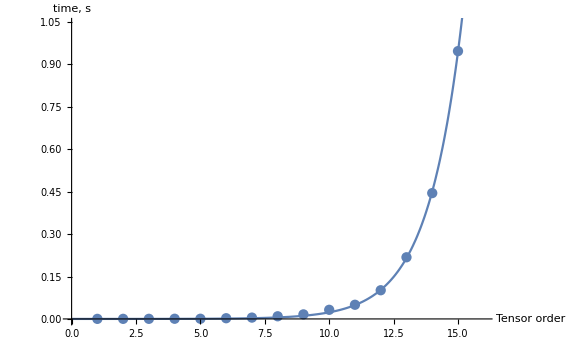

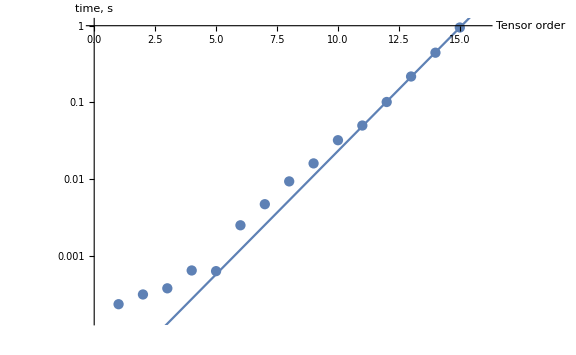

```mathematica
Table[Timing[ITensor[dummyArray[i]]][[1]],{i,1,15}];
τ Exp[t/T]/.FindFit[%,τ Exp[t/T],{τ,T},t];
Show[{ListPlot[%%,ImageSize->Large,AxesLabel->{"Tensor order","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%]+1},{0,1.1Max[%%]}}],Plot[%,{t,0,Length[%%]+2},PlotLegends->%]}]
Show[{ListLogPlot[%%%,ImageSize->Large,AxesLabel->{"Tensor order","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%%]+1},{0,1.1Max[%%%]}}],LogPlot[%%,{t,0,Length[%%%]+2},PlotLegends->%%]}]
```

C tensor.

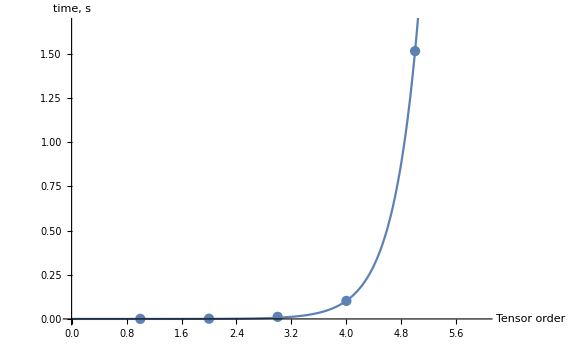

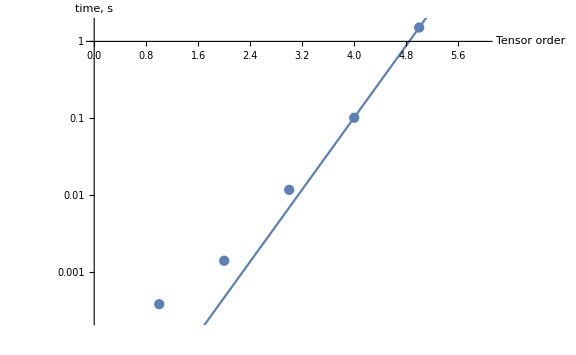

```mathematica
Table[Timing[CTensor[dummyArray[i]]][[1]],{i,1,5}];
τ Exp[t/T]/.FindFit[%,τ Exp[t/T],{τ,T},t];
Show[{ListPlot[%%,ImageSize->Large,AxesLabel->{"Tensor order","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%]+1},{0,1.1Max[%%]}}],Plot[%,{t,0,Length[%%]+2},PlotLegends->%]}]
Show[{ListLogPlot[%%%,ImageSize->Large,AxesLabel->{"Tensor order","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%%]+1},{0,1.1Max[%%%]}}],LogPlot[%%,{t,0,Length[%%%]+2},PlotLegends->%%]}]
```

CIII tensor.

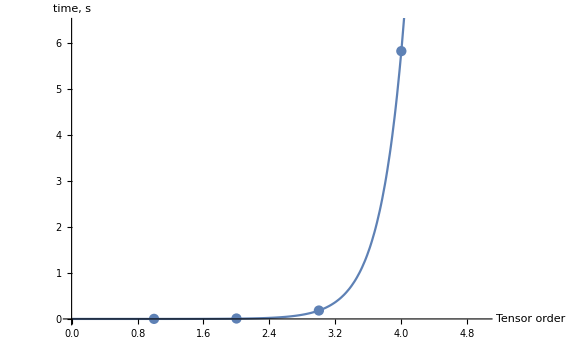

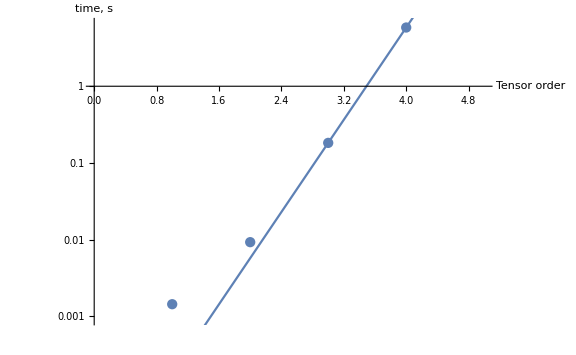

```mathematica
Table[Timing[CIIITensor[{μ,ν,α,β,ρ,σ},dummyArray[i]]][[1]],{i,1,4}];
τ Exp[t/T]/.FindFit[%,τ Exp[t/T],{τ,T},t];
Show[{ListPlot[%%,ImageSize->Large,AxesLabel->{"Tensor order","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%]+1},{0,1.1Max[%%]}}],Plot[%,{t,0,Length[%%]+2},PlotLegends->%]}]
Show[{ListLogPlot[%%%,ImageSize->Large,AxesLabel->{"Tensor order","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%%]+1},{0,1.1Max[%%%]}}],LogPlot[%%,{t,0,Length[%%%]+2},PlotLegends->%%]}]
```

Graviton vertex.

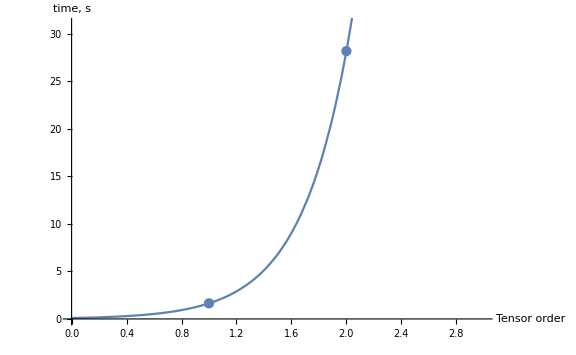

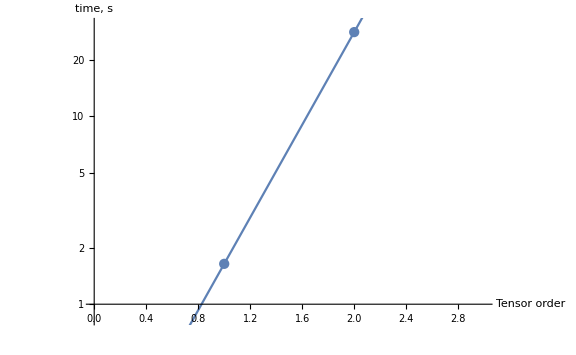

```mathematica
Table[Timing[GravitonVertex[Flatten[Function[{ToExpression["m"<>ToString[#]],ToExpression["n"<>ToString[#]],ToExpression["p"<>ToString[#]]}]/@Range[i]]]][[1]],{i,3,4}];
τ Exp[t/T]/.FindFit[%,τ Exp[t/T],{τ,T},t];
Show[{ListPlot[%%,ImageSize->Large,AxesLabel->{"Tensor order","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%]+1},{0,1.1Max[%%]}}],Plot[%,{t,0,Length[%%]+2},PlotLegends->%]}]
Show[{ListLogPlot[%%%,ImageSize->Large,AxesLabel->{"Tensor order","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%%]+1},{0,1.1Max[%%%]}}],LogPlot[%%,{t,0,Length[%%%]+2},PlotLegends->%%]}]
```

Graviton-scalar vertex.

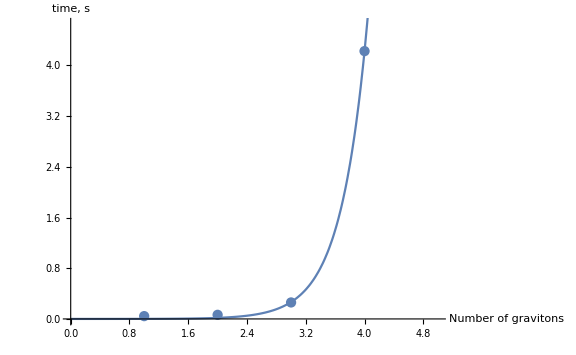

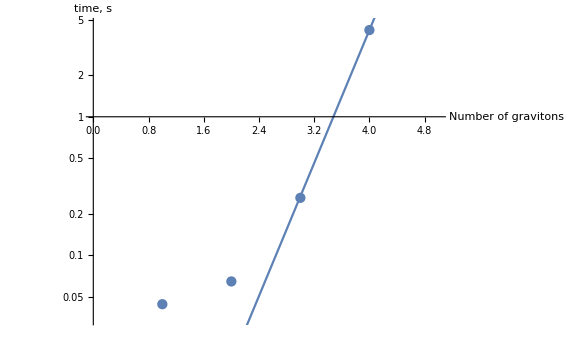

```mathematica
Table[Timing[GravitonScalarVertex[Join[dummyArray[i],{p1,p2}]]][[1]],{i,1,4}];
τ Exp[t/T]/.FindFit[%,τ Exp[t/T],{τ,T},t];
Show[{ListPlot[%%,ImageSize->Large,AxesLabel->{"Number of gravitons","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%]+1},{0,1.1Max[%%]}}],Plot[%,{t,0,Length[%%]+2},PlotLegends->%]}]
Show[{ListLogPlot[%%%,ImageSize->Large,AxesLabel->{"Number of gravitons","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%%]+1},{0,1.1Max[%%%]}}],LogPlot[%%,{t,0,Length[%%%]+2},PlotLegends->%%]}]
```

Graviton-vector vertex.

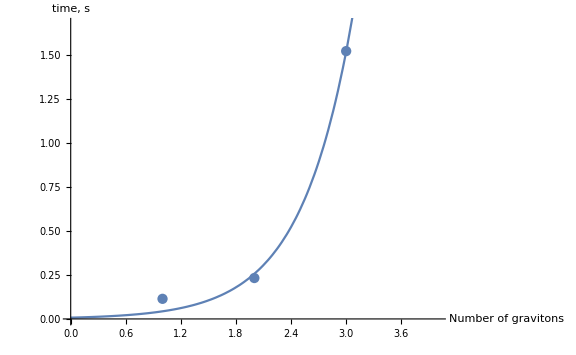

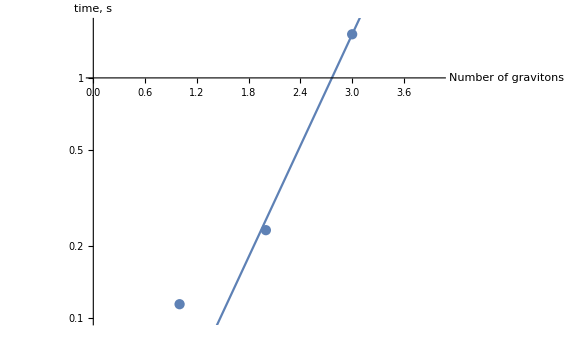

```mathematica
Table[Timing[GravitonVectorVertex[Join[dummyArray[i],{λ1,λ2,p1,p2}]]][[1]],{i,1,3}];
τ Exp[t/T]/.FindFit[%,τ Exp[t/T],{τ,T},t];
Show[{ListPlot[%%,ImageSize->Large,AxesLabel->{"Number of gravitons","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%]+1},{0,1.1Max[%%]}}],Plot[%,{t,0,Length[%%]+2},PlotLegends->%]}]
Show[{ListLogPlot[%%%,ImageSize->Large,AxesLabel->{"Number of gravitons","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%%]+1},{0,1.1Max[%%%]}}],LogPlot[%%,{t,0,Length[%%%]+2},PlotLegends->%%]}]
```

Graviton-fermion vertex.

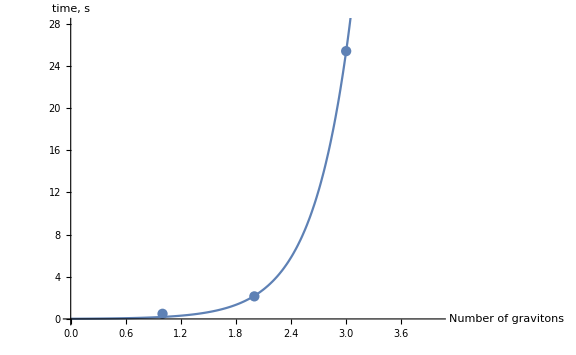

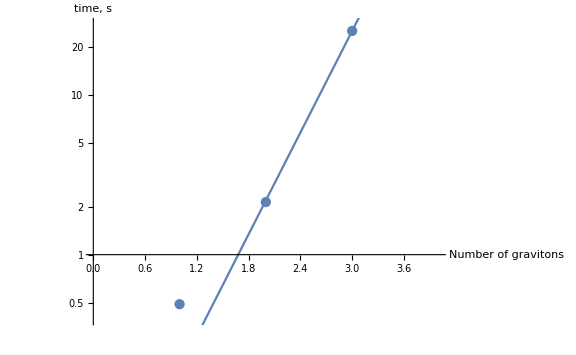

```mathematica
Table[Timing[GravitonFermionVertex[Join[dummyArray[i],{λ1,λ2,p1,p2}]]][[1]],{i,1,3}];
τ Exp[t/T]/.FindFit[%,τ Exp[t/T],{τ,T},t];
Show[{ListPlot[%%,ImageSize->Large,AxesLabel->{"Number of gravitons","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%]+1},{0,1.1Max[%%]}}],Plot[%,{t,0,Length[%%]+2},PlotLegends->%]}]
Show[{ListLogPlot[%%%,ImageSize->Large,AxesLabel->{"Number of gravitons","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%%]+1},{0,1.1Max[%%%]}}],LogPlot[%%,{t,0,Length[%%%]+2},PlotLegends->%%]}]
```

# Export procedures.

## Procedures that perform export of interaction vertices.

This command set the working directory to be the directory where this file is placed.

```mathematica
SetDirectory[NotebookDirectory[]]
```

/media/latosh/Borealis/Science/Wolfram_Packages/FeynGrav/Libs

Export of graviton vertices up to order 𝒪(κ^order).

```mathematica
exportGravitonVertex[order_] := Module[{cursor}, 
Print["Export of graviton vertices is initiated."];
For[cursor=3,cursor≤order+2,cursor++,
Evaluate[GravitonVertex[Flatten[Function[{ToExpression["m"<>ToString[#]],ToExpression["n"<>ToString[#]],ToExpression["p"<>ToString[#]]}]/@Range[cursor]]]]>>"GravitonVertex_"<>ToString[cursor-2];
Print["Done for order "<>ToString[cursor-2]];
]
]
```

Export of graviton-scalar vertices up to order 𝒪(κ^order).

```mathematica
exportGravitonScalarVertex[order_]:=Module[{cursor},
Print["Export of graviton-scalar vertices is initiated."];
	For[cursor=1,cursor<=order,cursor++,
	Evaluate[GravitonScalarVertex[Join[dummyArray[cursor],{p1,p2}]]]>>"GravitonScalarVertex_"<>ToString[cursor];
	Print["Done for order "<>ToString[cursor]];
	];
Print["Export of graviton-massive scalar vertices is initiated."];
	For[cursor=1,cursor<=order,cursor++,
	Evaluate[GravitonMassiveScalarVertex[Join[dummyArray[cursor],{p1,p2}],m]]>>"GravitonMassiveScalarVertex_"<>ToString[cursor];
	Print["Done for order "<>ToString[cursor]];
	];
]
```

Export of graviton-vector vertices up to order 𝒪(κ^order).

```mathematica
exportGravitonVectorVertex[order_]:=Module[{cursor},
	Print["Export of graviton-vector vertices is initiated."];
	For[cursor=1,cursor<=order,cursor++,
		Evaluate[GravitonVectorVertex[Join[dummyArray[cursor],{λ1,λ2,p1,p2}]]]>>"GravitonVectorVertex_"<>ToString[cursor];
		Print["Done for order "<>ToString[cursor]];
	];
Print["Export of graviton-massive vector vertices is initiated."];
	For[cursor=1,cursor<=order,cursor++,
		Evaluate[GravitonMassiveVectorVertex[Join[dummyArray[cursor],{λ1,λ2,p1,p2}],m]]>>"GravitonMassiveVectorVertex_"<>ToString[cursor];
		Print["Done for order "<>ToString[cursor]];
	]
]
```

Export of graviton-fermion vertices up to order 𝒪(κ^order).

```mathematica
exportGravitonFermionVertex[order_]:=Module[{cursor},
	Print["Export of graviton-fermion vertices is initiated."];
	For[cursor=1,cursor<=order,cursor++,
		Evaluate[GravitonFermionVertex[Join[dummyArray[cursor],{p1,p2}]]]>>"GravitonFermionVertex_"<>ToString[cursor];
		Print["Done for order "<>ToString[cursor]];
	]
Print["Export of graviton-massive fermion vertices is initiated."];
	For[cursor=1,cursor<=order,cursor++,
		Evaluate[GravitonMassiveFermionVertex[Join[dummyArray[cursor],{p1,p2}],m]]>>"GravitonMassiveFermionVertex_"<>ToString[cursor];
		Print["Done for order "<>ToString[cursor]];
	]
]
```

## The actual export. Do not run without a necessity!

The following module runs the export procedure. The export is performed up to the order 𝒪(κ^order).

```mathematica
Module[{order},
order =3;
exportGravitonVertex[order];
exportGravitonScalarVertex[order];
exportGravitonVectorVertex[order];
exportGravitonFermionVertex[order];
]
```

Export of graviton vertices is initiated.

Done for order 1

Done for order 2